## The Bridge Crossing Problem

### The Situation: A number of people arrive at a bridge and have to cross over to the other side. Each person takes a certain time to cross the bridge. The bridge can only handle two people walking over it at any one time. For any two people who cross the bridge, the time it takes is the time it takes for the slower person to cross the bridge. Moreover, a lantern is required to light the way and there is only one lantern. The Question: Given N people and the time it takes each person to cross the bridge, what is the minimum time it takes all N people to cross the bridge?

## 1) Prototype the steps individually

```mathematica
(* Initial States *)
people = {1,2,4,10};
initialState = people;
leftSide = initialState;
rightSide = {};
timeToCross = {};
```

```mathematica
(* Round 1 *)
```

```mathematica
(* Pick two people to cross from the initial state *)
toCross = RandomSample[leftSide,2]
```

{2,10}

```mathematica
leftSide = Complement[leftSide, toCross]
```

{1,4}

```mathematica
timeToCross = Append[timeToCross,Max[toCross]]
```

{10}

```mathematica
(* Of the two who crossed, pick one to cross back to carry the lamp *)
(* But before you do, check if the leftSide is {}; if yes, then the game is over *)
```

```mathematica
toCrossBack = If[leftSide ≠ {}, RandomChoice[toCross], Return["Game Over"]]
```

2

```mathematica
(* Add the time to cross back *)
```

```mathematica
timeToCross = Append[timeToCross, toCrossBack]
```

{10,2}

```mathematica
(* Who's on the left side? *)
leftSide = Union[leftSide, {toCrossBack}]
```

{1,2,4}

```mathematica
rightSide = Complement[initialState, leftSide]
```

{10}

```mathematica
(* End of Round 1 *)
```

```mathematica
Nest[f,{x1,x2, x3},3]
```

f[f[f[{x1,x2,x3}]]]

```mathematica
RandomChoice[{1,2}]
```

2

```mathematica
Complement[{2}, {2}]
```

{}

```mathematica
Append[{},2]
```

{2}

```mathematica
Union[{},{9,10}]
```

{9,10}

```mathematica
Complement[{a,b,c},{a,c,b}] == {}
```

True

```mathematica
l1 = {1,1,3,4,2,2};
l2 = {1,2,3,4,4,3,2,2,1};
```

## Diversion: Determining if two lists are equal when the lists are considered as sets -- i.e. the order of the elements doesn’t matter.

### See http://mathematica.stackexchange.com/questions/63617/check-if-two-lists-are-equal-in-any-order/105539#105539

```mathematica
AreListsEqual[list1_, list2_]:= If[Length[list1] ≥ Length[list2],Complement[list1,list2] == {}, Complement[list2,list1] == {}];
```

```mathematica
AreListsEqual[{a,b,c},{a,b,d}]
```

False

```mathematica
AreListsEqual[{a,b,c},{a,c,b,d}]
```

False

```mathematica
Complement[{a,b,c,c, f, f},{a,c,b, b, g, f}]
```

{}

```mathematica
Complement[{a,b,c,c, f, f}, {a,c,b, b, g, f}]
```

{}

```mathematica
Complement[{a,b}, {a,b,c}]
```

{}

```mathematica
Complement[{a,b,c}, {a,b}]
```

{c}

```mathematica
AreListsEqual2[list1_, list2_]:= Complement[list1,list2] == Complement[list2,list1];
```

```mathematica
AreListsEqual2[{a,b,c,c, f, f}, {a,c,b, b, g, f}]
```

False

```mathematica
AreListsEqual2[{a,a,b}, {a,b}]
```

True

```mathematica
Timing[AreListsEqual2[{a,c,b, b, g, f,e,e,e}, {a,e,b,c,c, f, f,g}]]
```

{0.000027,True}

```mathematica
RandomInteger[10^10]
```

5134438950

```mathematica
(* s1=DeleteDuplicates[RandomInteger[10^10,10^7]];
s2=Take[DeleteDuplicates[RandomInteger[10^10,2*10^7]],Length[s1]+1];
*)
```

```mathematica
Timing[AreListsEqual2[s1,s2]]
```

{10.0881,False}

```mathematica
AreListsEqual3[list1_, list2_]:= If[Length[list1] ≠ Length[list2],False, Complement[list1,list2] == Complement[list2,list1]];
```

```mathematica
Timing[AreListsEqual3[s1,s2]]
```

{0.000019,False}

```mathematica
(* s1=DeleteDuplicates[RandomInteger[10^10,10^7]];
s2=Take[DeleteDuplicates[RandomInteger[10^10,2*10^7]],Length[s1]+1];
*)
```

```mathematica
(* s3=RandomInteger[10^10,10^7];
s4=RandomInteger[10^10,10^7];
*)
```

```mathematica
Timing[AreListsEqual3[s3,s4]]
```

{10.0737,False}

```mathematica
ContainsAll[{a,c,b, b, g, f,e,e,e}, {a,e,b,c,c, f, f,g}]
```

True

```mathematica
l1
```

{1,1,3,4,2,2}

```mathematica
l2
```

{1,2,3,4,4,3,2,2,1}

```mathematica
SubsetQ[l2,l1]
```

True

```mathematica
AreListsEqual3[{a,b,c, a}, {a,a,b,c}]
```

True

## 2) Build a function to play any round of the game - prototype and test

```mathematica
bridgeCrossing[{initialState_, leftSideList_, rightSideList_, timeToCrossList_}]:= Module[{toCross, timeToCross, rightSide, leftSide, toCrossBack,timeToCrossEndState, leftSideEndState, rightSideEndState},

(* This function is built to be iterated -- that's why the inputs are a series of lists -- each iteration produces the next sequence of these lists *)
(* INPUT CHECKS *)
(* Check if the leftSideList is a subset of the initialState. If not, exit *)
If[Length[leftSideList] ≤ Length[initialState] && ContainsAll[initialState, leftSideList],True, Return["The second input must be a subset of the first input -- please try again."]];

(* Check if the rightSideList is compatible with the initialState and the leftSideList *)
(* If[Complement[rightSideList ,Complement[initialState, leftSideList]] ≠ {}, Return["The third input must be the complement of the first two"]];
*)
If[Length[Join[leftSideList, rightSideList]] ≤ Length[initialState] && ContainsAll[initialState, Join[leftSideList, rightSideList]], True, Return["The third input must be compatible with the first two"]];
(* END INPUT CHECKS *)

(* Check to see if leftSideList is empty; if it is, then the game is over *)
If[Length[leftSideList] == 0, Return[{initialState, leftSideList, rightSideList, timeToCrossList}]];

(* The game goes on... *)
(* Pick two people to cross from the left side *)
If[Length[leftSideList]== 1 || Length[leftSideList] == 2, toCross = leftSideList, toCross = RandomSample[leftSideList, 2]];

(* Time it takes to cross *)
timeToCross =  Append[timeToCrossList,Max[toCross]];

(* Update the rightSideList *)
rightSide = Union[rightSideList, toCross];

(* Update the leftSideList *)
leftSide = Complement[initialState, rightSide];

(* If everyone is safely over on the right side, then the rightSide is the same as the initialState and the game is over *)
If[AreListsEqual3[rightSide,initialState],  Return[{initialState, leftSide, rightSide, timeToCross}]];

(* If[Length[rightSide] == Length[initialState]&& Complement[rightSide,initialState] == Complement[rightSide,initialState],Return[{initialState, leftSide, rightSide, timeToCross}]]; *)

(* If not, then from the rightSide, pick one person to cross back to carry the lamp *)
toCrossBack = RandomChoice[rightSide];

(* Add the time of the crossing back *)
timeToCrossEndState = Append[timeToCross, toCrossBack];

(* Add the person who crossed over to the leftSide *)
leftSideEndState = Union[leftSide, {toCrossBack}];

(* Remove the person who crossed back over from the rightSide *)
rightSideEndState = Complement[initialState, leftSideEndState];

{initialState, leftSideEndState, rightSideEndState, timeToCrossEndState}
];
```

```mathematica
bridgeCrossing[{{3,2,2,10}, {3}, {2,2, 2}, {}}]
```

{{3,2,2,10},{2,10},{3},{3,2}}

```mathematica
AreListsEqual3[{3,2,2,10}, Join[{3},{2,2,10}]]
```

True

```mathematica
Complement[{3,2,2,10}, {3,2}]
```

{10}

```mathematica
Nest[bridgeCrossing, {{3,2, 6,10}, {3,2,6,10}, {}, {}},4]
```

{{3,2,6,10},{},{2,3,6,10},{6,6,10,2,6}}

```mathematica
NestList[bridgeCrossing, {{1,2,9,10}, {1,9,10}, {2}, {1,2}}, 2]
```

{{{1,2,9,10},{1,9,10},{2},{1,2}},{1,10},bridgeCrossing[{1,10}]}

```mathematica
Min[Total[#] & /@ (Table[NestWhile[bridgeCrossing, {{3,2,1,10}, {3,2,1,10}, {}, {}},Length[#[[2]]] ≠ 0 &] ,5000][[All,4]])]
```

17

```mathematica
NestWhile[bridgeCrossing,{ {1,2,9,10}, {1,2,9,10}, {}, {}},Length[#[[2]]] ≠ 0 &]
```

$Aborted

```mathematica
NestWhile[bridgeCrossing, {{3,2,6,10}, {3,2,6,10}, {}, {}},Length[#[[2]]] ≠ 0 &]
```

```mathematica
(* Rewrite using ContainsAll and related functions for generality *)
```

## Generalizations

1) Any number of people to cross
2) Two people can take the same time to cross
3) More than 2 people can cross at the same time (this might make the solution much easier!)
4) Non-integer times for crossing

## 3) Build the function for real

```mathematica
areListsEqual[list1_, list2_]:= Tally[Sort[list1]] == Tally[Sort[list2]];
```

```mathematica
areListsEqual[{1,1,1,2}, {1,2,2,2}]
```

False

```mathematica
bridgeCrossingRound[{initialState_, leftSideList_, rightSideList_, timeToCrossList_}]:= Module[{toCross, toCrossPositions, toCrossPositionsFinal, timeToCross, rightSide, leftSide, toCrossBack,timeToCrossEndState, leftSideEndState, rightSideEndState},

(* This function is built to be iterated -- that's why the inputs are a series of lists -- each iteration produces the next sequence of these lists *)

(* INPUT CHECKS *)

(* The intialState cannot be empty *)
If[Length[initialState] == 0, Return["The first input - the initial state cannot be empty. Please try again."]];

(* The leftSideList, the rightSideList, and the initialState must make sense together *)
If[areListsEqual[initialState, Join[leftSideList, rightSideList]], True, Return["The second and third inputs must be compatible with each other and the first. Please try again."]];

(* END INPUT CHECKS *)

(* Check to see if leftSideList is empty; if it is, then the game is over *)
If[Length[leftSideList] == 0, Return[{initialState, leftSideList, rightSideList, timeToCrossList}]];

(* The game can be played another round... *)
(* Pick two people to cross from the left side *)
If[Length[leftSideList]== 1 || Length[leftSideList] == 2, toCross = leftSideList, toCross = RandomSample[leftSideList, 2]];

(* Find the positions of the people picked *)
toCrossPositions = Flatten[Position[leftSideList, #] &/@ toCross];

(* Just need the first two positions *)
If[Length[toCrossPositions] > 2, toCrossPositionsFinal = Take[toCrossPositions, 2], toCrossPositionsFinal = toCrossPositions];

Return[{leftSideList, toCross,toCrossPositions, toCrossPositionsFinal}];

(* Time it takes to cross *)
timeToCross =  Append[timeToCrossList,Max[toCross]];

(* Update the rightSideList *)
rightSide = Join[rightSideList, toCross];

(* Update the leftSideList *)
(* leftSide = Complement[initialState, rightSide]; *)
leftSide = leftSideList /. 

(* If everyone is safely over on the right side, then the rightSide is the same as the initialState and the game is over *)
If[areListsEqual[rightSide,initialState],  Return[{initialState, leftSide, rightSide, timeToCross}]];

(* If not, then from the rightSide, pick one person to cross back to carry the lamp *)
toCrossBack = RandomChoice[rightSide];

(* Add the time of the crossing back *)
timeToCrossEndState = Append[timeToCross, toCrossBack];

(* Add the person who crossed over to the leftSide *)
leftSideEndState = Union[leftSide, {toCrossBack}];

(* Remove the person who crossed back over from the rightSide *)
rightSideEndState = Complement[initialState, leftSideEndState];

{initialState, leftSideEndState, rightSideEndState, timeToCrossEndState}
];
```

```mathematica
Cases[{1,0,2,0,3},Except[0] && Except[2]]
```

{}

```mathematica
{1,0,2,0,3} //. x_/; x == 0 -> Nothing
```

{1,2,3}

```mathematica
bridgeCrossingRound[{{3,2,2,10}, {3,10,2,2}, {}, {}}]
```

{{3,10,2,2},{2,10},{3,4,2},{3,4}}

```mathematica
Nest[bridgeCrossing, {{3,2, 6,10}, {3,2,6,10}, {}, {}},4]
```

```mathematica
NestWhile[bridgeCrossing, {{3,2,6,10}, {3,2,6,10}, {}, {}},Length[#[[2]]] ≠ 0 &]
```

## After 2 tries, realized that it’s much easier to program if we complicate the input a bit -- so that’s the tradeoff: make the input a bit more complex and the logic becomes simpler. It’s a worthwhile tradeoff in this case because it easily enables generalization.

```mathematica
Cases[Tally[{a,a,b,b,c}][[All,2]], Except[1]]
```

{2,2}

## 4) Build the function with a more complicated input.

```mathematica
bridgeCrossingNew[{initialState_, leftSideList_, rightSideList_, timeToCrossList_, peopleToCrossList_}]:= Module[{toCross, toCrossPositions, toCrossPositionsFinal, timeToCross, peopleToCross, rightSide, leftSide, toCrossBack,timeToCrossEndState, leftSideEndState, rightSideEndState, peopleToCrossEndState},

(* This function is built to be iterated -- that's why the inputs are a series of lists -- each iteration produces the next sequence of these lists *)

(* The timeToCrossList and the peopleToCross list should initially both be {}. *)

(* *********INPUT CHECKS*********** *)
(* The intialState must be an Association *)
If[AssociationQ[initialState],True, Return["The first input must contain pairs - the name of the person and the time it takes the person to cross the bridge. Please try again."]];

(* The leftSideList, the rightSideList, and the initialState must make sense together *)

(* The leftSideList must be a subset of the keys of the initial state *)
If[SubsetQ[Keys[initialState], leftSideList], True, Return["The second input, the left side list, must be a subset of the names in the first input - the initial state. Please try again."]];

(* The leftSideList cannot contain any repeated names *)
If[Length[Cases[Tally[leftSideList][[All,2]], Except[1]]] == 0, True, Return["The second input cannot repeat any names. Please try again."]];

(* The rightSideList must be a complement of the keys of the initial state and the leftSideList *)
If[Length[Complement[rightSideList,Complement[Keys[initialState],leftSideList]]] == 0, True, Return["The third input, the right side list, must be a complement of the intial set of names and the left side list. Please try again."]];

(* The rightSideList cannot contain any repeated names *)
If[Length[Cases[Tally[rightSideList][[All,2]], Except[1]]] == 0, True, Return["The third input -- the right side list -- cannot repeat any names. Please try again."]];
(* *******END INPUT CHECKS********* *)

(* Check to see if leftSideList is empty; if it is, then the game is over *)
If[Length[leftSideList] == 0, Return[{initialState, leftSideList, rightSideList, timeToCrossList, peopleToCrossList}]];

(* If the leftSideList is not empty, the game can be played another round... *)
(* Pick two people to cross from the left side *)
If[Length[leftSideList]== 1 || Length[leftSideList] == 2, toCross = leftSideList, toCross = RandomSample[leftSideList, 2]];

(* Time it takes to cross *)
timeToCross =  Append[timeToCrossList,Max[Lookup[initialState, #] & /@ toCross]];

(* ADD List of People who have crossed *)
peopleToCross = Append[peopleToCrossList, toCross];

(* Update the rightSideList *)
rightSide = Union[rightSideList, toCross];

(* Update the leftSideList *)
leftSide = Complement[Keys[initialState], rightSide];

(* If everyone is safely over on the right side, then the rightSide is the same as the initialState and the game is over *)
If[Complement[Keys[initialState], rightSide] == {},  Return[{initialState, leftSide, rightSide, timeToCross, peopleToCross}]];

(* If not, then from the rightSide, pick one person to cross back to carry the lamp *)
toCrossBack = RandomChoice[rightSide];

(* Add the time of the crossing back *)
timeToCrossEndState = Append[timeToCross, Lookup[initialState,toCrossBack]];

(* ADD PeopleCrossedEndState *)
peopleToCrossEndState = Append[peopleToCross, toCrossBack];

(* Add the person who crossed over to the leftSide *)
leftSideEndState = Union[leftSide, {toCrossBack}];

(* Remove the person who crossed back over from the rightSide *)
rightSideEndState = Complement[Keys[initialState], leftSideEndState];

{initialState, leftSideEndState, rightSideEndState, timeToCrossEndState, peopleToCrossEndState}
];
```

```mathematica
bridgeCrossingNew[{<|a -> 1,b -> 2,c -> 9,d -> 10, e -> 15|>, {a,b,c,d, e}, {},{}, {}}]
```

{<|a→1,b→2,c→9,d→10,e→15|>,{a,b,d,e},{c},{9,2},{{b,c},b}}

```mathematica
init = <| a-> 1, b-> 2, c-> 9, d-> 10 |>;
```

```mathematica
Keys[init]
```

{a,b,c,d}

```mathematica
Nest[bridgeCrossingNew,{<|a -> 1,b -> 2,c -> 9,d -> 10, e -> 15|>, {a,b,c,d, e}, {},{}, {}}, 4]
```

{<|a→1,b→2,c→9,d→10,e→15|>,{},{a,b,c,d,e},{15,15,9,9,15,15,15},{{b,e},e,{a,c},c,{d,e},e,{c,e}}}

```mathematica
bridgeCrossingNew[{<|a->1,b->2,c->9,d->10,e->15|>,{b,c,d,e},{a},{2,2}, {}}]
```

{<|a→1,b→2,c→9,d→10,e→15|>,{b,c,e},{a,d},{2,2,15,15},{{d,e},e}}

```mathematica
NestWhile[bridgeCrossingNew,{<|a->1,b->2,c->2,d->11,e->11|>,{a,b,c,d,e},{},{}, {}},Length[#[[2]]] ≠ 0 &]
```

{<|a→1,b→2,c→2,d→11,e→11|>,{},{a,b,c,d,e},{11,1,2,2,11,2,2},{{d,a},a,{b,c},c,{c,e},b,{a,b}}}

```mathematica
Min[Total[#] & /@ (Table[NestWhile[bridgeCrossingNew, {<|a->1,b->2,c->9,d->10,e->15|>,{a,b,c,d,e},{},{}},Length[#[[2]]] ≠ 0 &] ,1000][[All,4]])]
```

33

```mathematica
Min[Total[#] & /@ Table[NestWhile[bridgeCrossingNew, {<|a->1,b->2,c->9,d->10|>,{a,b,c,d},{},{}},Length[#[[2]]] ≠ 0 &] ,5000][[All,4]]]
```

17

## BridgeCrossingMC

### A Monte Carlo simulation of the bridge crossing game. Several games are played and the outcomes are recorded.

```mathematica
bridgeCrossingMC[initialState_,leftSideList_, rightSideList_, timeToCrossList_, peopleToCrossList_]:= Module[{nTrials = 2000, totalInitialStateTime, allInfo, timesToCross, minTime, maxTime, minTimePositions, maxTimePositions, minTimeConfigs, maxTimeConfigs, output}, 
 (* Produces the minimum time it takes to cross the bridge based on a Monte Carlo simulation of n random trials *)

totalInitialStateTime = Total[Values[initialState]];

(* Also keeps the information on the end state of each of the trials *)
allInfo = Table[NestWhile[bridgeCrossingNew,{initialState,leftSideList, rightSideList, timeToCrossList, peopleToCrossList} ,Length[#[[2]]] ≠ 0 &] ,nTrials];
timesToCross = Total[#] & /@ allInfo[[All,4]];
minTime = Min[timesToCross];
(* Positions of the min times *)
minTimePositions = Flatten[Position[timesToCross, minTime]];
maxTime = Max[timesToCross];
(* Positions of the max times *)
maxTimePositions = Flatten[Position[timesToCross, maxTime]];

minTimeConfigs = allInfo[[minTimePositions]] // DeleteDuplicates;
maxTimeConfigs = allInfo[[maxTimePositions]] // DeleteDuplicates;

output = {totalInitialStateTime, minTime, maxTime, initialState,minTimeConfigs, maxTimeConfigs}
];
```

```mathematica
bridgeCrossingMC[<|a->1,b->2,c->9|>,{a,b,c},{},{}, {}]
```

{12,12,27,<|a→1,b→2,c→9|>,{{<|a→1,b→2,c→9|>,{},{a,b,c},{9,1,2},{{a,c},a,{a,b}}},{<|a→1,b→2,c→9|>,{},{a,b,c},{9,1,2},{{c,a},a,{a,b}}},{<|a→1,b→2,c→9|>,{},{a,b,c},{2,1,9},{{a,b},a,{a,c}}},{<|a→1,b→2,c→9|>,{},{a,b,c},{2,1,9},{{b,a},a,{a,c}}}},{{<|a→1,b→2,c→9|>,{},{a,b,c},{9,9,9},{{a,c},c,{b,c}}},{<|a→1,b→2,c→9|>,{},{a,b,c},{9,9,9},{{b,c},c,{a,c}}},{<|a→1,b→2,c→9|>,{},{a,b,c},{9,9,9},{{c,b},c,{a,c}}},{<|a→1,b→2,c→9|>,{},{a,b,c},{9,9,9},{{c,a},c,{b,c}}}}}

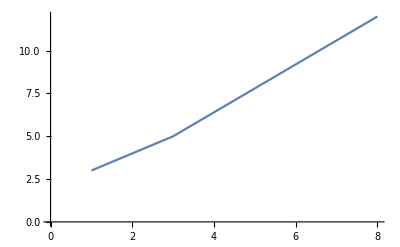

```mathematica
ListLinePlot[{{1,3}, {3,5}, {8,12}}]
```

## bridgeCrossingNew and bridgeCrossingMC give us a way to study the bridge crossing problem more intensely.

## In order to begin the study, we need to generate large sets of initial conditions. In order to do this, we’ll use a list of names of babies born in NYC in 2011 (https://data.cityofnewyork.us/resource/25th-nujf.json)

## To get the baby names, run the NYCBabyNames.nb notebook.

## We’ll build the inputs by the number of people initially on the left side of the bridge.

```mathematica
names = nycBNnm // DeleteDuplicates
```

{ABIGAIL,ADA,AISHA,AIZA,ALEENA,ALEXA,ALEXANDRA,ALICE,ALINA,ALISHA,ALIYAH,ALLISON,ALYSSA,AMANDA,AMBER,AMELIA,AMY,ANGEL,ANGELA,ANGELINA,ANGIE,ANIKA,ANNA,ANNABELLE,ANNIE,ARIA,ARIANA,ARIANNA,ARYA,ASHLEY,AUDREY,AVA,AYESHA,BELLA,BONNIE,BRIANNA,CATHERINE,CECILIA,CHARLOTTE,CHLOE,CHRISTINA,CHRISTINE,CHRISTY,CINDY,CLAIRE,CYNTHIA,DAISY,DIYA,EILEEN,ELAINE,ELENA,ELINA,ELIZABETH,ELLA,EMILY,EMMA,ERICA,ERIKA,ERIN,ESHAL,EVA,EVELYN,FATIMA,FIONA,GIANNA,GRACE,HAILEY,HANNAH,HELEN,IRENE,IRIS,ISABEL,ISABELLA,ISABELLE,IVY,JANICE,JANNAT,JASMINE,JENNIFER,JENNY,JESSICA,JESSIE,JIA,JOANNA,JOCELYN,JOY,JOYCE,JULIA,KAITLYN,KAREN,KATE,KATELYN,KATHERINE,KATIE,KAYLA,KAYLEE,KELLY,KHLOE,KYLIE,LAUREN,LEAH,LEELA,LILLIAN,LILY,MADISON,MAGGIE,MANDY,MARYAM,MAYA,MEGAN,MELODY,MIA,MICHELLE,MILA,MINA,NATALIE,NICOLE,NINA,OLIVIA,PHOEBE,QUEENIE,RACHEL,RAINA,REBECCA,RENEE,SABRINA,SAMANTHA,SARA,SARAH,SELENA,SELINA,SERENA,SHARON,SHIRLEY,SOFIA,SOPHIA,SOPHIE,STELLA,STEPHANIE,SYEDA,TANISHA,TENZIN,TIFFANY,TINA,VANESSA,VICKY,VICTORIA,VIVIAN,WENDY,WINNIE,XIN,YU,ZAHRA,ZAINAB,ZARA,ZOE,AALIYAH,ADDISON,AICHA,AISSATOU,ALANA,ALEXIS,ALICIA,AMANI,AMAYA,AMINA,AMINATA,AMIRA,AMIRAH,AMIYAH,ANAYA,ANIYA,ANIYAH,ARIEL,ARIELLE,AUBREY,AUTUMN,BRIELLE,BROOKE,CAMILLE,CHELSEA,CHEYENNE,DAKOTA,DANIELLE,DESTINY,DYLAN,EDEN,EGYPT,ESSENCE,FAITH,FANTA,FATOU,FATOUMATA,GABRIELLA,GABRIELLE,GENESIS,HARMONY,HAWA,HEAVEN,IMANI,JADA,JADE,JALIYAH,JANELLE,JANIYA,JANIYAH,JAYDA,JAYLA,JORDYN,KAI,KALIYAH,KAMIYAH,KELSEY,KENDRA,KENNEDY,KENYA,KIARA,KIMORA,KYLA,LAILA,LAYLA,LEILANI,LONDON,LONDYN,LYRIC,MACKENZIE,MAKAYLA,MALIA,MALIYAH,MARIAH,MARIAM,MARIAMA,MCKENZIE,MELANIE,MIKAYLA,MILAN,MORGAN,MYA,NADIA,NAHLA,NANA,NAOMI,NATALIA,NEVAEH,NIA,NYLA,NYLAH,PAIGE,PARIS,PEYTON,PRINCESS,RILEY,SADE,SAMARA,SAMIYA,SAMIYAH,SANAA,SANAI,SANIYA,SANIYAH,SARAI,SARIAH,SASHA,SAVANNAH,SERENITY,SHANIA,SHANIYA,SHILOH,SKYE,SKYLA,SKYLAR,SORAYA,SUMMER,SYDNEY,SYMPHONY,TABITHA,TAMIA,TARAJI,TAYLOR,TIANA,TIANNA,TORI,TRINITY,ZAHARA,ZANIYAH}

```mathematica
(* For a given list of names, set up an initial state for the bridge crossing problem *)
```

```mathematica
threeState = Association[Transpose[{RandomSample[names, 3], RandomInteger[{1,30}, 3]}]/. {x_,y_} -> {x -> y}]
```

<|KAMIYAH→14,BONNIE→19,HANNAH→21|>

```mathematica
buildInitialState[nameList_, numPeople_, minTimeToCross_, maxTimeToCross_]:= Association[Transpose[{RandomSample[nameList, numPeople], RandomInteger[{minTimeToCross,maxTimeToCross}, numPeople]}]/. {x_,y_} -> {x -> y}];
```

```mathematica
buildInitialState[names,4,1,30]
```

<|SYEDA→5,ELAINE→21,SKYLAR→25,SANIYA→29|>

```mathematica
bridgeCrossingInput[nameList_, numPeople_, minTimeToCross_, maxTimeToCross_]:= Module[{initialState, leftSideList, input},
initialState = Association[Transpose[{RandomSample[nameList, numPeople], RandomInteger[{minTimeToCross,maxTimeToCross}, numPeople]}]/. {x_,y_} -> {x -> y}];
leftSideList = Keys[initialState];
input = Sequence[initialState, leftSideList, {}, {}, {}]
];
```

```mathematica
bridgeCrossingMC[bridgeCrossingInput[names,8,1,30]]
```

{116,132,325,<|NANA→15,ANNIE→2,ANIYAH→24,REBECCA→23,PEYTON→16,JOCELYN→26,MYA→6,ANIYA→4|>,{{<|NANA→15,ANNIE→2,ANIYAH→24,REBECCA→23,PEYTON→16,JOCELYN→26,MYA→6,ANIYA→4|>,{},{ANIYA,ANIYAH,ANNIE,JOCELYN,MYA,NANA,PEYTON,REBECCA},{26,6,15,6,4,2,6,6,23,2,6,6,24},{{JOCELYN,MYA},MYA,{MYA,NANA},MYA,{ANNIE,ANIYA},ANNIE,{ANNIE,MYA},MYA,{PEYTON,REBECCA},ANNIE,{ANNIE,MYA},MYA,{ANIYAH,MYA}}}},{{<|NANA→15,ANNIE→2,ANIYAH→24,REBECCA→23,PEYTON→16,JOCELYN→26,MYA→6,ANIYA→4|>,{},{ANIYA,ANIYAH,ANNIE,JOCELYN,MYA,NANA,PEYTON,REBECCA},{26,26,24,24,26,23,24,26,26,26,26,24,24},{{JOCELYN,REBECCA},JOCELYN,{ANNIE,ANIYAH},ANIYAH,{JOCELYN,PEYTON},REBECCA,{ANIYAH,ANIYA},JOCELYN,{REBECCA,JOCELYN},JOCELYN,{MYA,JOCELYN},ANIYAH,{ANIYAH,NANA}}}}}

## One more function, and we’re ready to do some analysis

```mathematica
(* Just output the total time for all the people at the start of the crossing, the min time and the max time *)
bridgeCrossingMCAbridged[initialState_,leftSideList_, rightSideList_, timeToCrossList_, peopleToCrossList_]:= bridgeCrossingMC[initialState,leftSideList, rightSideList, timeToCrossList, peopleToCrossList][[1;;4]];
```

```mathematica
bridgeCrossingMCAbridged[bridgeCrossingInput[names,8,1,30]]
```

{133,143,378,<|SARAI→4,TENZIN→14,HAWA→29,KENNEDY→3,ELINA→30,AMY→6,KENYA→27,JAYDA→20|>}

## Case 1: Three people -- the simplest case for this problem

```mathematica
(* Create a list of inputs -- start with 50 of them *)
```

```mathematica
threePersonInputs = Table[bridgeCrossingInput[names, 3, 1, 10], 5][[1]]
```

<|KYLIE→4,KAYLA→9,CATHERINE→2|>

```mathematica
(* Run the abridged Monte Carlo to see how the 3-person crossing behaves *)
```

```mathematica
outputs3 = Table[bridgeCrossingMCAbridged[bridgeCrossingInput[names,3,1,10]], 25]// Sort
```

{{7,7,9,<|KHLOE→2,ZOE→2,CAMILLE→3|>},{8,8,9,<|HEAVEN→2,KAITLYN→3,ALEXIS→3|>},{10,10,15,<|HAILEY→2,CHLOE→3,DESTINY→5|>},{10,10,24,<|KATELYN→8,MELANIE→1,JAYLA→1|>},{11,11,18,<|GRACE→6,MEGAN→4,IVY→1|>},{12,12,21,<|FATOUMATA→4,SHANIA→7,RILEY→1|>},{13,13,24,<|SHILOH→4,KIARA→1,JANIYAH→8|>},{13,13,30,<|RENEE→10,ESSENCE→2,KYLA→1|>},{14,14,15,<|JORDYN→5,SASHA→4,MEGAN→5|>},{14,14,18,<|ALEXANDRA→6,PEYTON→3,XIN→5|>},{15,15,24,<|ALLISON→2,ARIELLE→8,MARIAH→5|>},{15,15,24,<|ANNA→5,JENNY→2,ISABELLE→8|>},{16,16,24,<|HEAVEN→3,MILAN→5,KAITLYN→8|>},{17,17,21,<|ANGELINA→3,JENNIFER→7,HAWA→7|>},{17,17,30,<|SORAYA→5,ALYSSA→2,SKYE→10|>},{18,18,27,<|AMINATA→9,ADDISON→3,LEELA→6|>},{18,18,27,<|SANAA→1,LAILA→9,TAMIA→8|>},{18,18,30,<|DAKOTA→2,ALISHA→10,ALICE→6|>},{19,19,24,<|KATE→5,SHIRLEY→8,SERENA→6|>},{23,23,24,<|SOPHIE→7,NIA→8,MIKAYLA→8|>},{23,23,30,<|TIANA→7,LEAH→6,KATHERINE→10|>},{24,24,30,<|SERENITY→9,AICHA→5,KENYA→10|>},{24,24,30,<|TAYLOR→6,EVELYN→8,ANGEL→10|>},{25,25,30,<|ALEXIS→10,JESSIE→5,ABIGAIL→10|>},{28,28,30,<|VIVIAN→9,GABRIELLA→9,XIN→10|>}}

### It’s quite clear that the minimum time is always equal to the sum of the times it takes each person to cross the bridge individually. The maximum time depends - it can vary based on how the initial times were distributed amongst the bridge crossers.

```mathematica
(* Plot the minimum and maximum times as a function of the total initial time *)
```

```mathematica
min3 = {#[[1]], #[[2]]} & /@ outputs3
```

{{7,7},{8,8},{10,10},{10,10},{11,11},{12,12},{13,13},{13,13},{14,14},{14,14},{15,15},{15,15},{16,16},{17,17},{17,17},{18,18},{18,18},{18,18},{19,19},{23,23},{23,23},{24,24},{24,24},{25,25},{28,28}}

```mathematica
max3 = {#[[1]], #[[3]]} & /@ outputs3
```

{{7,9},{8,9},{10,15},{10,24},{11,18},{12,21},{13,24},{13,30},{14,15},{14,18},{15,24},{15,24},{16,24},{17,21},{17,30},{18,27},{18,27},{18,30},{19,24},{23,24},{23,30},{24,30},{24,30},{25,30},{28,30}}

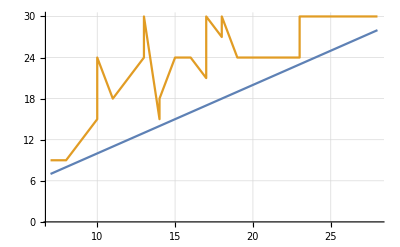

```mathematica
p3 = ListLinePlot[{min3, max3}, GridLines->Automatic]
```

## Case 2: Four people

```mathematica
(* Run the abridged Monte Carlo with 25 randomly generated inputs to see how the 4-person crossing behaves *)
```

```mathematica
outputs4 = Table[bridgeCrossingMCAbridged[bridgeCrossingInput[names,4,1,10]], 25]// Sort
```

{{13,14,30,<|KENNEDY→6,CAMILLE→1,GABRIELLE→3,SKYLA→3|>},{14,15,25,<|BELLA→1,TANISHA→4,ANGELINA→4,AMIRA→5|>},{15,14,35,<|SKYE→1,CHELSEA→2,AUDREY→5,SANAA→7|>},{15,15,40,<|AMANDA→2,JALIYAH→4,ARIANA→8,AISHA→1|>},{17,18,40,<|PAIGE→3,LYRIC→1,JULIA→5,ERIN→8|>},{18,19,50,<|ZANIYAH→10,PARIS→1,ZOE→3,CHEYENNE→4|>},{19,16,45,<|VICKY→7,CINDY→2,ANIKA→9,DYLAN→1|>},{19,20,45,<|CHLOE→5,KYLIE→4,KENNEDY→9,KAITLYN→1|>},{19,21,45,<|CATHERINE→9,TENZIN→2,AMELIA→4,TAYLOR→4|>},{22,23,50,<|AMINA→10,JADA→6,ALEXANDRA→5,JANELLE→1|>},{22,25,40,<|MICHELLE→6,ZANIYAH→3,TABITHA→5,NEVAEH→8|>},{23,21,50,<|ZAINAB→8,TORI→2,ALLISON→10,MARIAH→3|>},{23,25,40,<|MAKAYLA→6,ALIYAH→8,CHRISTINA→7,FATOU→2|>},{24,22,50,<|OLIVIA→3,ELLA→3,ANNABELLE→10,JOANNA→8|>},{24,26,40,<|AMIYAH→2,AMBER→8,GIANNA→8,ELINA→6|>},{25,26,50,<|JAYLA→6,TIANNA→8,DAISY→10,ANGELINA→1|>},{25,27,40,<|ESHAL→8,ELLA→4,JANNAT→5,LAUREN→8|>},{26,27,45,<|IRIS→9,SADE→8,ZAHARA→1,SAMANTHA→8|>},{26,27,50,<|LILY→9,KAITLYN→5,ESSENCE→2,DAKOTA→10|>},{26,28,45,<|ERIKA→7,ARIEL→2,NICOLE→9,SYMPHONY→8|>},{26,31,45,<|MAKAYLA→6,DAISY→6,KAYLEE→9,GABRIELLA→5|>},{28,32,45,<|LONDYN→8,HAILEY→4,AMANDA→9,ASHLEY→7|>},{30,35,45,<|BRIANNA→8,EVA→8,SHANIYA→9,CYNTHIA→5|>},{31,35,50,<|AYESHA→10,KHLOE→8,ANNIE→4,ZAHARA→9|>},{31,36,50,<|KENNEDY→10,AMINA→5,JASMINE→7,BRIANNA→9|>}}

### We see that both the minimum and maximum times in this case can vary based on is how the initial times were distributed amongst the bridge crossers.

```mathematica
(* Plot the minimum and maximum times as a function of the total initial time *)
```

```mathematica
min4 = {#[[1]], #[[2]]} & /@ outputs4
```

{{13,14},{14,15},{15,14},{15,15},{17,18},{18,19},{19,16},{19,20},{19,21},{22,23},{22,25},{23,21},{23,25},{24,22},{24,26},{25,26},{25,27},{26,27},{26,27},{26,28},{26,31},{28,32},{30,35},{31,35},{31,36}}

```mathematica
max4 = {#[[1]], #[[3]]} & /@ outputs4
```

{{13,30},{14,25},{15,35},{15,40},{17,40},{18,50},{19,45},{19,45},{19,45},{22,50},{22,40},{23,50},{23,40},{24,50},{24,40},{25,50},{25,40},{26,45},{26,50},{26,45},{26,45},{28,45},{30,45},{31,50},{31,50}}

```mathematica
init4 = {#[[1]], #[[1]]} & /@ outputs4
```

{{13,13},{14,14},{15,15},{15,15},{17,17},{18,18},{19,19},{19,19},{19,19},{22,22},{22,22},{23,23},{23,23},{24,24},{24,24},{25,25},{25,25},{26,26},{26,26},{26,26},{26,26},{28,28},{30,30},{31,31},{31,31}}

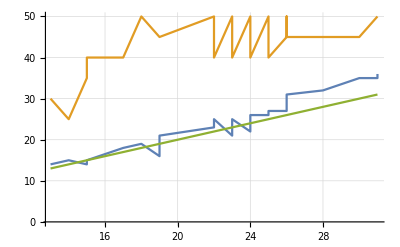

```mathematica
p4 = ListLinePlot[{min4, max4, init4}, GridLines->Automatic]
```

### It' s very interesting that the minimum times can be *less* than the total initial times! This happens whenever the blue line crosses below the green line. Most of the time, the minimum time is +1 or =2 of the

## Case 3: Five People

```mathematica
outputs5 = Table[bridgeCrossingMCAbridged[bridgeCrossingInput[names,5,1,10]], 25]// Sort
```

{{13,13,35,<|ZANIYAH→5,SKYE→1,LEELA→3,JANIYAH→3,BELLA→1|>},{17,19,70,<|ALICIA→2,JIA→2,MALIYAH→2,ERIKA→10,ZOE→1|>},{18,19,49,<|STEPHANIE→1,RACHEL→4,EVELYN→7,JASMINE→2,JANIYAH→4|>},{20,18,70,<|PRINCESS→1,ALICE→5,SHIRLEY→3,ALEXIS→10,KAYLA→1|>},{23,25,70,<|SAMIYA→1,JULIA→3,PAIGE→10,FANTA→5,EMILY→4|>},{24,25,63,<|NIA→5,SHANIA→1,KENDRA→3,FATIMA→6,AISHA→9|>},{25,23,70,<|GRACE→2,MIA→1,AMY→10,ZAHRA→5,CHELSEA→7|>},{25,27,70,<|HARMONY→4,HAWA→6,ADDISON→4,GENESIS→10,CATHERINE→1|>},{26,26,56,<|AIZA→8,STELLA→3,VIVIAN→5,FIONA→8,SELINA→2|>},{26,30,70,<|ZANIYAH→4,HANNAH→4,TENZIN→10,EVELYN→6,ZAINAB→2|>},{26,32,63,<|JADE→9,LEELA→5,SHANIA→5,LILY→3,AMAYA→4|>},{27,25,63,<|ALICIA→3,LYRIC→5,ISABELLA→9,KATELYN→1,MILAN→9|>},{27,27,70,<|TABITHA→10,FAITH→2,CHEYENNE→4,ANNIE→8,WINNIE→3|>},{28,30,63,<|KATE→8,JANIYAH→5,ALEXA→1,JOANNA→9,GIANNA→5|>},{29,31,56,<|KYLA→6,TAMIA→8,JADA→7,ZARA→1,SAMANTHA→7|>},{29,37,63,<|JOANNA→6,JANIYAH→5,JAYLA→5,ZOE→9,JANNAT→4|>},{30,34,63,<|SANAI→9,MARIAMA→5,SANAA→6,KENYA→8,JORDYN→2|>},{31,33,63,<|TIANA→5,EGYPT→9,ISABEL→9,KATHERINE→1,PRINCESS→7|>},{31,33,70,<|LAYLA→10,LYRIC→8,JANICE→7,KATHERINE→4,CLAIRE→2|>},{32,34,63,<|MILA→6,KYLA→1,SAMARA→9,SHIRLEY→9,FANTA→7|>},{32,35,70,<|NAHLA→5,DANIELLE→2,JOCELYN→9,KALIYAH→10,MAKAYLA→6|>},{33,35,63,<|AMIRAH→9,ARIANNA→9,GRACE→7,AUBREY→1,EVA→7|>},{34,38,63,<|SELENA→8,ZAHRA→9,KAYLA→2,AMINATA→8,KENNEDY→7|>},{35,36,70,<|MALIA→3,WENDY→4,SAMANTHA→10,MIKAYLA→8,WINNIE→10|>},{36,48,56,<|KIARA→7,JENNY→8,GRACE→7,JORDYN→8,MYA→6|>}}

```mathematica
(* Plot the minimum and maximum times as a function of the total initial time *)
```

```mathematica
min5 = {#[[1]], #[[2]]} & /@ outputs5
```

{{13,13},{17,19},{18,19},{20,18},{23,25},{24,25},{25,23},{25,27},{26,26},{26,30},{26,32},{27,25},{27,27},{28,30},{29,31},{29,37},{30,34},{31,33},{31,33},{32,34},{32,35},{33,35},{34,38},{35,36},{36,48}}

```mathematica
max5 = {#[[1]], #[[3]]} & /@ outputs5
```

{{13,35},{17,70},{18,49},{20,70},{23,70},{24,63},{25,70},{25,70},{26,56},{26,70},{26,63},{27,63},{27,70},{28,63},{29,56},{29,63},{30,63},{31,63},{31,70},{32,63},{32,70},{33,63},{34,63},{35,70},{36,56}}

```mathematica
init5 = {#[[1]], #[[1]]} & /@ outputs5
```

{{13,13},{17,17},{18,18},{20,20},{23,23},{24,24},{25,25},{25,25},{26,26},{26,26},{26,26},{27,27},{27,27},{28,28},{29,29},{29,29},{30,30},{31,31},{31,31},{32,32},{32,32},{33,33},{34,34},{35,35},{36,36}}

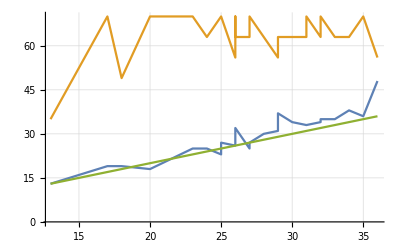

```mathematica
p5 = ListLinePlot[{min5, max5, init5}, GridLines->Automatic]
```

## Case 4: Six People

```mathematica
outputs6 = Table[bridgeCrossingMCAbridged[bridgeCrossingInput[names,6,1,10]], 25]// Sort
```

{{22,23,52,<|PAIGE→1,SAMARA→5,JADE→3,AMAYA→2,QUEENIE→5,GABRIELLE→6|>},{22,23,75,<|SABRINA→1,BONNIE→2,ALYSSA→9,TIANA→6,NIA→2,ARIANNA→2|>},{22,24,72,<|FATOUMATA→4,LEELA→8,MELODY→1,DAKOTA→2,JESSICA→5,TABITHA→2|>},{25,25,54,<|ALISHA→4,NEVAEH→6,GIANNA→6,CHRISTINE→2,TARAJI→1,JAYDA→6|>},{26,31,72,<|SOPHIA→8,ELAINE→3,NINA→3,NAOMI→2,ABIGAIL→4,JADA→6|>},{27,30,90,<|CECILIA→1,KATIE→10,JOANNA→3,SORAYA→3,NANA→6,KYLA→4|>},{29,29,82,<|SERENITY→1,JANNAT→6,NANA→10,MADISON→2,TAYLOR→6,BELLA→4|>},{32,34,79,<|ELENA→2,AMBER→9,IVY→6,AMAYA→3,KATELYN→8,JENNY→4|>},{32,34,86,<|ALEENA→6,EDEN→8,SASHA→4,MINA→10,LONDON→1,KAMIYAH→3|>},{32,39,90,<|ALEXA→3,NEVAEH→6,AIZA→4,SAMIYAH→3,ASHLEY→10,KAITLYN→6|>},{32,41,82,<|KENYA→4,EGYPT→6,ALANA→5,TINA→3,LAYLA→4,SELINA→10|>},{33,35,81,<|ELLA→2,SABRINA→3,MARIAMA→3,ARIANA→9,IVY→9,GENESIS→7|>},{35,32,81,<|EDEN→7,IRIS→9,ALEENA→1,NINA→2,MORGAN→7,SELENA→9|>},{35,32,88,<|FAITH→9,NAOMI→9,SARIAH→1,MYA→10,EMMA→2,SASHA→4|>},{35,38,81,<|ANGELINA→2,QUEENIE→8,JIA→7,LILLIAN→9,KELSEY→3,NEVAEH→6|>},{37,40,90,<|AALIYAH→6,ALISHA→8,JENNY→8,ASHLEY→3,MAYA→10,SYDNEY→2|>},{39,46,90,<|AICHA→7,BRIANNA→5,EILEEN→7,NATALIE→8,TAMIA→2,JOCELYN→10|>},{40,49,81,<|LAYLA→6,FAITH→3,ELLA→9,JASMINE→8,ARIA→5,PARIS→9|>},{40,52,90,<|ELLA→7,AMAYA→10,PAIGE→4,LEILANI→5,VICKY→7,KAI→7|>},{41,42,90,<|ELIZABETH→3,ELINA→10,ANIKA→6,AMINATA→2,SUMMER→10,SARAI→10|>},{41,49,90,<|SAMIYA→5,KATIE→6,EMILY→10,KENYA→7,KAMIYAH→10,NATALIE→3|>},{44,43,90,<|MEGAN→9,ANNABELLE→4,LEAH→9,SABRINA→2,ELAINE→10,EDEN→10|>},{44,54,90,<|SAMIYA→5,ISABELLE→8,DESTINY→8,DYLAN→10,KIMORA→10,FATIMA→3|>},{45,57,90,<|NEVAEH→7,ALANA→10,SADE→7,LYRIC→3,LEAH→8,JANIYA→10|>},{46,52,90,<|ADA→8,AMAYA→10,KATE→2,EMMA→10,KYLA→7,DAISY→9|>}}

```mathematica
(* Plot the minimum and maximum times as a function of the total initial time *)
```

```mathematica
min6 = {#[[1]], #[[2]]} & /@ outputs6
```

{{22,23},{22,23},{22,24},{25,25},{26,31},{27,30},{29,29},{32,34},{32,34},{32,39},{32,41},{33,35},{35,32},{35,32},{35,38},{37,40},{39,46},{40,49},{40,52},{41,42},{41,49},{44,43},{44,54},{45,57},{46,52}}

```mathematica
max6 = {#[[1]], #[[3]]} & /@ outputs6
```

{{22,52},{22,75},{22,72},{25,54},{26,72},{27,90},{29,82},{32,79},{32,86},{32,90},{32,82},{33,81},{35,81},{35,88},{35,81},{37,90},{39,90},{40,81},{40,90},{41,90},{41,90},{44,90},{44,90},{45,90},{46,90}}

```mathematica
init6 = {#[[1]], #[[1]]} & /@ outputs6
```

{{22,22},{22,22},{22,22},{25,25},{26,26},{27,27},{29,29},{32,32},{32,32},{32,32},{32,32},{33,33},{35,35},{35,35},{35,35},{37,37},{39,39},{40,40},{40,40},{41,41},{41,41},{44,44},{44,44},{45,45},{46,46}}

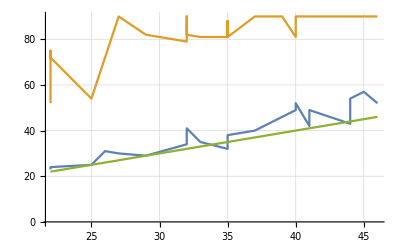

```mathematica
p6 = ListLinePlot[{min6, max6, init6}, GridLines->Automatic]
```

### As the number of people goes up, the chance of having a minimum time that’s lower than the total initial time gets higher and higher (seems to be).

## Case 5: Seven People

```mathematica
outputs7 = Table[bridgeCrossingMCAbridged[bridgeCrossingInput[names,7,1,10]], 25]// Sort
```

{{21,22,79,<|ELINA→2,MAYA→1,KIMORA→1,AUDREY→2,CYNTHIA→5,KATELYN→2,ASHLEY→8|>},{27,30,77,<|EGYPT→1,JOCELYN→5,AMIRA→2,MADISON→7,DYLAN→2,DESTINY→3,JANNAT→7|>},{28,26,96,<|EDEN→5,TIANA→1,XIN→2,LEAH→2,ALICE→7,FATOUMATA→10,MILAN→1|>},{28,29,91,<|ANGEL→1,BONNIE→4,EVA→8,LILY→2,AIZA→1,MARIAM→3,AUDREY→9|>},{30,33,100,<|KATELYN→1,AISSATOU→7,AMANDA→2,FATOUMATA→2,MICHELLE→10,ZAINAB→3,EDEN→5|>},{31,36,83,<|ISABELLE→8,JOANNA→5,OLIVIA→5,VIVIAN→3,VICTORIA→2,AMY→6,ERICA→2|>},{31,36,91,<|MCKENZIE→9,ANGELINA→7,KAYLEE→3,ELENA→3,EGYPT→2,NATALIE→2,GABRIELLE→5|>},{31,38,90,<|DESTINY→5,SHILOH→9,ZAHARA→4,MADISON→4,TENZIN→4,MALIYAH→4,NATALIA→1|>},{32,34,97,<|MALIYAH→1,JAYDA→8,AUBREY→7,MORGAN→2,KELLY→9,TRINITY→2,ANGELA→3|>},{32,38,98,<|TABITHA→10,IRENE→6,LONDON→2,SANAI→4,MAYA→4,HARMONY→4,NEVAEH→2|>},{34,32,110,<|BONNIE→3,EVELYN→10,TORI→4,ANAYA→10,ANGELA→2,ISABELLA→4,MALIYAH→1|>},{34,37,91,<|ALEXA→2,ALINA→2,RAINA→2,KIMORA→7,VICKY→5,JANICE→7,IRIS→9|>},{36,43,104,<|SYMPHONY→5,JOANNA→2,KAYLEE→4,ERIKA→10,AMELIA→7,JADA→3,JASMINE→5|>},{37,42,110,<|JESSICA→5,BELLA→8,SANIYA→6,KENDRA→10,BONNIE→3,JANIYA→3,SHANIA→2|>},{37,45,103,<|AALIYAH→3,KELSEY→4,ISABELLA→4,ZAINAB→6,HAWA→10,CYNTHIA→7,JOYCE→3|>},{38,39,95,<|CHEYENNE→4,MIA→7,KHLOE→2,ALICE→9,TIFFANY→7,PEYTON→1,ANGELINA→8|>},{38,40,105,<|KELSEY→2,NANA→10,SASHA→5,HAWA→7,IRIS→8,MEGAN→5,DESTINY→1|>},{39,46,88,<|KELLY→4,FANTA→7,LAYLA→8,DESTINY→6,NAOMI→5,PARIS→1,SOFIA→8|>},{40,45,99,<|SADE→9,EVELYN→4,MIA→7,KAI→7,SAMARA→3,ISABELLE→9,BROOKE→1|>},{42,48,106,<|ARIELLE→6,ISABELLA→7,PEYTON→4,CHELSEA→10,GENESIS→9,JOANNA→1,BROOKE→5|>},{43,50,106,<|BROOKE→8,TAYLOR→1,ALIYAH→6,WENDY→9,TENZIN→10,JESSICA→4,JANELLE→5|>},{44,55,106,<|NAOMI→4,NIA→4,ASHLEY→4,JORDYN→9,MICHELLE→10,LYRIC→9,ESSENCE→4|>},{44,57,102,<|VIVIAN→6,ANIKA→2,JANNAT→6,KELSEY→10,BRIANNA→7,FAITH→5,SOPHIA→8|>},{50,63,106,<|BROOKE→9,CHRISTINA→2,ERIKA→8,CHRISTY→6,ALEENA→10,GIANNA→8,AUBREY→7|>},{50,68,104,<|HARMONY→9,CHARLOTTE→7,NYLA→10,SYDNEY→5,LONDYN→4,AMIYAH→8,PAIGE→7|>}}

```mathematica
(* Plot the minimum and maximum times as a function of the total initial time *)
```

```mathematica
min7 = {#[[1]], #[[2]]} & /@ outputs7
```

{{21,22},{27,30},{28,26},{28,29},{30,33},{31,36},{31,36},{31,38},{32,34},{32,38},{34,32},{34,37},{36,43},{37,42},{37,45},{38,39},{38,40},{39,46},{40,45},{42,48},{43,50},{44,55},{44,57},{50,63},{50,68}}

```mathematica
max7 = {#[[1]], #[[3]]} & /@ outputs7
```

{{21,79},{27,77},{28,96},{28,91},{30,100},{31,83},{31,91},{31,90},{32,97},{32,98},{34,110},{34,91},{36,104},{37,110},{37,103},{38,95},{38,105},{39,88},{40,99},{42,106},{43,106},{44,106},{44,102},{50,106},{50,104}}

```mathematica
init7 = {#[[1]], #[[1]]} & /@ outputs7
```

{{21,21},{27,27},{28,28},{28,28},{30,30},{31,31},{31,31},{31,31},{32,32},{32,32},{34,34},{34,34},{36,36},{37,37},{37,37},{38,38},{38,38},{39,39},{40,40},{42,42},{43,43},{44,44},{44,44},{50,50},{50,50}}

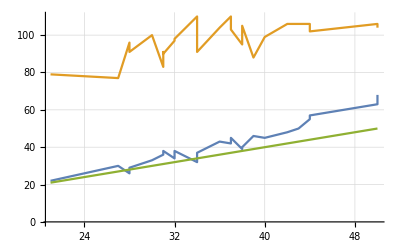

```mathematica
p7 = ListLinePlot[{min7, max7, init7}, GridLines->Automatic]
```

## Case 6: 100 People

### CAUTION: Very long computation - run only as needed

```mathematica
outputs100 = Table[bridgeCrossingMCAbridged[bridgeCrossingInput[names,100,1,10]], 25]// Sort
```

{{453,926,1167,<|ANGELINA→3,AMINATA→3,AMY→8,KAI→6,JOANNA→3,CAMILLE→7,ALLISON→5,NATALIA→1,DIYA→4,LYRIC→3,EMMA→5,ANNABELLE→10,KIMORA→1,WENDY→5,MILAN→3,FANTA→6,ZARA→3,SOPHIA→7,MAYA→9,ESSENCE→1,BONNIE→5,AMELIA→3,SAVANNAH→2,CHRISTINE→9,NANA→2,WINNIE→5,AMBER→2,ADA→4,DAKOTA→4,AUDREY→8,MADISON→5,SANIYA→1,EGYPT→5,EDEN→6,CINDY→6,JESSICA→5,EILEEN→9,JASMINE→9,ARIANNA→9,KAITLYN→2,LAILA→8,KATIE→2,MYA→10,ADDISON→9,ALINA→10,MELODY→4,JANIYAH→1,JORDYN→1,ANGELA→2,SAMANTHA→3,TABITHA→7,MEGAN→6,DAISY→7,TARAJI→1,ANNIE→3,AYESHA→4,TIANA→4,ALICIA→5,CATHERINE→3,CHELSEA→6,RACHEL→1,ARIANA→2,JANELLE→10,JADA→7,KYLA→1,NINA→4,ERIN→1,FATOUMATA→6,AMIRAH→9,AVA→5,SORAYA→4,MARIAH→3,LAYLA→4,ISABELLA→4,NIA→3,AMIRA→3,SANIYAH→1,SAMIYA→4,SABRINA→6,STELLA→8,AMANI→4,SARA→2,JANNAT→2,ERICA→2,BELLA→6,KIARA→6,GENESIS→3,ANAYA→5,PRINCESS→7,BRIANNA→8,YU→6,SKYLA→6,MAGGIE→1,AUTUMN→5,STEPHANIE→2,ANIYA→1,JENNIFER→6,ZAINAB→1,HELEN→2,ASHLEY→2|>},{495,1016,1270,<|OLIVIA→5,SERENA→10,SANIYA→7,AISHA→6,FATIMA→7,TRINITY→3,BELLA→10,CINDY→5,PRINCESS→7,JIA→8,PHOEBE→2,EVA→5,MILA→6,HELEN→7,AMY→7,MINA→10,ZAHRA→4,TIANA→3,KAYLA→9,HAWA→2,TIFFANY→8,TANISHA→4,JOANNA→3,FAITH→3,MIKAYLA→5,NYLA→1,AALIYAH→2,SHARON→5,JOCELYN→2,ALINA→9,ANIKA→1,ALEENA→10,ANNABELLE→10,JOY→6,YU→5,NAHLA→7,ANNIE→3,MANDY→1,MAYA→7,NIA→1,GENESIS→7,ALYSSA→4,SANAA→7,CHEYENNE→1,IMANI→5,SAVANNAH→2,EVELYN→5,ANGEL→1,ARIELLE→7,EILEEN→1,ARIA→3,ARIANNA→2,ARIEL→10,ELAINE→6,CHRISTINA→6,MORGAN→2,JORDYN→4,SARAI→1,MILAN→5,GRACE→9,AVA→2,SARIAH→2,SOFIA→8,SYMPHONY→6,AISSATOU→4,KELLY→10,TENZIN→9,QUEENIE→1,CHARLOTTE→10,CLAIRE→3,MELODY→8,ANAYA→5,ALICE→4,FATOU→3,MARIAMA→8,NAOMI→9,ALICIA→3,KALIYAH→6,VICTORIA→3,LYRIC→3,CATHERINE→4,SELENA→5,ERICA→5,SAMIYAH→2,ERIN→5,LONDYN→1,HAILEY→2,IVY→2,LEILANI→1,MACKENZIE→8,KAREN→8,ARYA→1,ZAINAB→6,DIYA→3,SHANIYA→5,ISABEL→3,BROOKE→6,FIONA→5,ELINA→9,AUDREY→3|>},{514,987,1327,<|AMANDA→10,BROOKE→1,GIANNA→4,AUDREY→5,LEILANI→6,GENESIS→5,ALIYAH→1,SASHA→6,SARA→3,NYLA→8,AALIYAH→2,ANGELINA→7,NICOLE→9,DIYA→7,GABRIELLA→2,ANGIE→8,SUMMER→9,TARAJI→2,ANNABELLE→3,ANIKA→2,DANIELLE→2,IVY→3,SYEDA→3,HELEN→7,ESHAL→7,AISSATOU→7,KELSEY→8,MARIAMA→9,ABIGAIL→5,JOYCE→3,SARIAH→2,JANNAT→3,FATOUMATA→2,ALICE→3,ZAINAB→7,MACKENZIE→10,FIONA→1,PARIS→4,EVA→6,SOPHIE→2,MALIYAH→5,CLAIRE→6,ZARA→10,IMANI→6,ELENA→3,KENDRA→1,ISABEL→1,DAISY→9,ISABELLA→10,JALIYAH→3,TANISHA→8,NAOMI→3,CHRISTINA→1,NANA→10,VICKY→3,SYDNEY→7,SHANIA→8,FATIMA→4,SKYLA→2,LILLIAN→4,GABRIELLE→8,STELLA→7,VANESSA→4,CHEYENNE→5,MARIAH→9,ANGEL→1,DAKOTA→10,CYNTHIA→5,JULIA→5,TAMIA→10,LILY→3,JADA→3,ALISHA→6,MIKAYLA→8,AUBREY→6,IRENE→5,MEGAN→8,SOPHIA→4,ARIANNA→1,ANNA→2,ARIELLE→3,ASHLEY→4,SAMARA→6,YU→8,SERENA→6,EDEN→10,JANIYAH→9,PEYTON→3,ALEXANDRA→8,SHARON→4,AYESHA→2,NATALIA→1,AISHA→3,ALANA→9,ANGELA→4,SAMIYAH→9,IRIS→3,SORAYA→1,ALEENA→3,SADE→10|>},{514,1033,1334,<|AUDREY→6,SELINA→5,KYLIE→10,ELENA→4,SYEDA→1,YU→4,TANISHA→4,GENESIS→9,CECILIA→9,SANIYAH→4,SAVANNAH→10,MICHELLE→8,PHOEBE→7,ANAYA→1,IRIS→10,SABRINA→2,JOYCE→7,ESHAL→4,DAISY→4,JALIYAH→10,ELLA→10,ANIKA→5,NAHLA→10,FAITH→2,JANICE→8,BROOKE→5,SARAI→3,MIKAYLA→4,VIVIAN→3,ALEXIS→2,ZAHRA→5,ADA→2,SAMIYA→6,ARYA→5,MCKENZIE→4,LEILANI→10,ARIA→8,NATALIE→1,TARAJI→9,MADISON→1,SANAA→4,DANIELLE→1,TIANA→8,SELENA→5,ALICIA→8,NINA→3,CHEYENNE→7,OLIVIA→7,AVA→2,ALANA→2,PAIGE→8,JAYDA→9,HEAVEN→1,ISABELLE→4,NICOLE→3,PEYTON→10,AMIYAH→3,LAILA→2,IMANI→10,SARAH→10,TENZIN→6,SHANIA→2,SYDNEY→7,ZOE→1,KYLA→4,ALISHA→2,KENNEDY→1,MORGAN→1,KENDRA→6,ANNA→8,MARYAM→3,ANGELINA→4,ALEXANDRA→2,SAMARA→1,KAMIYAH→6,ELIZABETH→6,JANIYA→7,ANIYAH→2,AMAYA→9,HELEN→1,TRINITY→1,GABRIELLE→6,SHARON→8,KAITLYN→6,CLAIRE→10,JANELLE→3,MARIAMA→10,ARIANA→4,KAYLEE→2,MAKAYLA→6,LEAH→2,SUMMER→3,SERENITY→8,CHLOE→2,CATHERINE→8,LAUREN→7,AMINA→10,KIARA→2,EVELYN→4,KENYA→4|>},{524,1018,1309,<|KAREN→4,ELLA→10,MADISON→5,MYA→7,BROOKE→4,ELAINE→5,MANDY→3,JOANNA→2,AIZA→3,ALANA→4,QUEENIE→5,NANA→10,JORDYN→4,ZANIYAH→4,NYLAH→2,ARIEL→5,RACHEL→10,SAMARA→3,EVELYN→3,REBECCA→2,SANIYA→3,SHILOH→9,BELLA→3,ADA→4,CINDY→4,LILLIAN→1,ZAHARA→7,JANNAT→8,SASHA→8,WENDY→10,DAKOTA→8,KENYA→2,FIONA→4,MILA→1,BONNIE→10,TAYLOR→7,DANIELLE→1,ALEENA→5,MARYAM→7,ANNABELLE→5,CHRISTINE→7,KIMORA→3,CHELSEA→4,CAMILLE→3,AMINATA→4,LILY→3,LEAH→5,SKYLAR→8,STEPHANIE→8,SHANIA→7,AYESHA→2,ANNA→10,NAHLA→4,JESSIE→6,AICHA→3,ANIYAH→2,TINA→8,SHANIYA→10,AMIRA→3,MAYA→10,OLIVIA→2,MELODY→9,SELENA→3,JALIYAH→8,STELLA→7,ALICIA→1,LEILANI→6,TABITHA→6,RILEY→10,NATALIA→5,SARA→10,FANTA→6,SARIAH→4,KAI→8,KAMIYAH→4,ANNIE→3,ERIKA→9,ARYA→1,SAMIYAH→3,ARIANNA→6,ALICE→1,VICTORIA→10,LONDYN→2,SARAH→4,JENNIFER→3,ELENA→2,SARAI→7,KYLIE→8,EILEEN→4,ZOE→4,ERICA→6,AMINA→10,KAITLYN→5,EVA→10,ALLISON→1,AMAYA→5,MICHELLE→3,TIANA→5,AMANDA→8,DAISY→3|>},{528,1070,1341,<|LYRIC→1,GABRIELLE→9,AUDREY→2,AISSATOU→6,ADDISON→9,ANGEL→4,ANIKA→5,ISABELLA→7,ALYSSA→2,KHLOE→4,IVY→7,WENDY→1,MARIAMA→3,FATOUMATA→2,KATE→9,ALEENA→4,KALIYAH→5,BELLA→1,GIANNA→10,HAILEY→1,MYA→4,ELIZABETH→10,TIFFANY→1,ARIA→3,AMINATA→9,HANNAH→8,ANNABELLE→3,SUMMER→2,SHILOH→1,FAITH→9,BONNIE→9,TINA→9,ARIANA→1,ESHAL→8,LONDYN→4,SOPHIA→8,ZANIYAH→9,ALEXIS→7,SANAI→10,SASHA→5,ZAHARA→9,ANNA→1,MIKAYLA→7,MALIA→3,ALISHA→9,RENEE→7,NAOMI→7,ANGELINA→1,LAYLA→4,KAREN→5,KAYLA→5,GENESIS→5,LEAH→3,MARYAM→4,IMANI→4,JORDYN→4,MARIAH→2,SANIYA→1,ARYA→5,JAYLA→6,JALIYAH→9,MADISON→1,ERIN→6,DYLAN→10,AMBER→9,SERENITY→8,MAGGIE→6,AMANI→5,MORGAN→2,BRIANNA→1,IRIS→4,DIYA→7,NATALIA→4,JULIA→1,VANESSA→5,CHRISTINA→3,RACHEL→6,LONDON→7,JANNAT→6,SARAI→5,JANELLE→5,OLIVIA→7,STEPHANIE→8,KIARA→8,ZOE→1,KENNEDY→3,NAHLA→2,ALICE→8,ELLA→3,JENNIFER→9,PRINCESS→5,NATALIE→4,REBECCA→5,HEAVEN→8,ARIANNA→10,TIANA→5,CLAIRE→7,KELLY→9,JOYCE→5,SYDNEY→7|>},{529,1074,1354,<|ANGELA→7,LYRIC→9,GRACE→1,KATIE→9,DANIELLE→4,ISABELLE→9,ALEXIS→5,ABIGAIL→6,NYLAH→7,MARYAM→6,ZANIYAH→2,IRENE→9,SYEDA→3,SOPHIE→3,LONDON→3,CLAIRE→4,SAVANNAH→2,ALICIA→5,SELENA→9,KENYA→1,DAKOTA→10,JANELLE→2,TORI→10,ZAINAB→3,EILEEN→2,REBECCA→1,CHRISTINE→1,ESSENCE→2,HAWA→7,ARIANA→1,AMINATA→9,ANAYA→6,CHRISTY→5,FIONA→8,SAMANTHA→7,TENZIN→1,KAYLA→3,MEGAN→1,AALIYAH→1,JAYDA→7,EGYPT→2,AUBREY→8,JOY→9,RAINA→8,HANNAH→3,FATOUMATA→5,ANNABELLE→3,ANGIE→8,LEAH→8,MILA→8,STEPHANIE→5,MORGAN→10,MIKAYLA→10,RACHEL→2,MARIAMA→4,YU→4,LAUREN→6,AMAYA→8,NEVAEH→3,EMILY→4,ISABELLA→10,EVA→1,AMELIA→1,LILLIAN→1,NINA→4,TIANA→2,AMIYAH→8,MACKENZIE→7,ZAHRA→1,NADIA→3,JASMINE→7,ELLA→7,MELODY→10,JAYLA→7,TANISHA→4,MANDY→4,ANIYA→1,HEAVEN→2,TABITHA→7,JULIA→7,LONDYN→10,QUEENIE→8,MADISON→7,NATALIA→10,ERIKA→10,KIMORA→3,ELIZABETH→2,SORAYA→9,KAREN→7,JESSICA→9,SOPHIA→2,KENNEDY→1,AMINA→2,PHOEBE→6,SERENITY→5,EDEN→5,TRINITY→3,MARIAH→9,JALIYAH→10,KHLOE→8|>},{533,1101,1386,<|EGYPT→1,AMAYA→4,TENZIN→7,ANGIE→8,ELINA→3,OLIVIA→9,TINA→2,SUMMER→2,KHLOE→2,KENDRA→1,SAMARA→6,MAGGIE→10,NATALIE→10,SELINA→5,CLAIRE→4,GABRIELLA→3,NADIA→10,PAIGE→4,SOPHIA→10,YU→2,ANIYAH→2,MALIYAH→4,TANISHA→8,MORGAN→8,ZAINAB→5,SAVANNAH→2,KIARA→3,MIKAYLA→4,JADA→10,AMINA→8,SANAI→4,CINDY→9,NEVAEH→10,SARAH→4,AVA→8,IRIS→4,IMANI→8,JENNIFER→1,ALICE→8,RACHEL→4,ERIKA→8,DANIELLE→9,HARMONY→1,NYLA→10,DESTINY→3,NATALIA→6,VIVIAN→7,CHEYENNE→6,NIA→1,JESSIE→5,LILY→1,VANESSA→6,ALIYAH→7,ESSENCE→3,SHARON→8,NANA→3,HELEN→1,SKYE→7,PEYTON→7,ADA→2,IVY→9,ISABELLE→8,ALANA→8,KAITLYN→2,LONDON→10,JANIYA→1,JANICE→4,KAREN→9,KYLIE→4,ALLISON→10,KAMIYAH→3,BROOKE→4,HAILEY→9,DAISY→7,FATIMA→10,ZAHRA→4,TRINITY→5,LYRIC→6,VICTORIA→7,LILLIAN→1,BELLA→6,SKYLA→1,AIZA→1,NINA→5,AMIRAH→2,SARIAH→4,ZANIYAH→3,KELLY→5,SOPHIE→3,JULIA→3,ADDISON→10,MARIAH→5,CHRISTINA→6,GENESIS→2,RENEE→6,SHANIYA→10,MALIA→7,ANIYA→3,SANAA→2,ANIKA→10|>},{536,1065,1348,<|SARA→2,SASHA→9,ALICIA→8,TINA→4,KAYLA→3,AICHA→10,NYLAH→1,ERIN→3,SERENA→8,TENZIN→1,SAMARA→4,LILLIAN→7,TIFFANY→9,KIARA→3,RENEE→3,MANDY→5,NAOMI→7,LEILANI→3,NADIA→6,IVY→5,MIKAYLA→7,MELANIE→2,SHILOH→6,LAUREN→4,BRIANNA→2,GABRIELLA→1,NIA→3,LONDYN→3,ALYSSA→5,NAHLA→9,TRINITY→5,CAMILLE→10,MINA→4,FANTA→9,CHLOE→5,XIN→6,EVELYN→9,KHLOE→4,NEVAEH→4,TAYLOR→2,AMIRAH→8,BONNIE→5,YU→10,PRINCESS→9,DESTINY→5,TAMIA→7,CHRISTINA→3,IMANI→9,MALIA→9,JASMINE→10,JOY→5,HARMONY→9,GABRIELLE→6,ZAHRA→4,CHARLOTTE→3,TIANNA→7,LYRIC→2,SHIRLEY→10,SUMMER→3,RILEY→1,CINDY→1,MAGGIE→9,MILAN→9,SELINA→4,JULIA→7,SARAH→1,AMANI→4,BRIELLE→7,ANIYAH→7,ISABELLA→10,JANICE→3,AMINA→6,CATHERINE→10,SYMPHONY→1,ANIYA→6,DAISY→4,CLAIRE→2,KAREN→9,JENNY→4,ZARA→2,SABRINA→1,KAMIYAH→5,GENESIS→7,ISABEL→3,MARIAH→10,ARIEL→4,ERICA→4,PEYTON→9,ESHAL→1,AMELIA→1,ELAINE→10,AMBER→4,HANNAH→3,SANAA→1,AMAYA→3,ELINA→6,ALIYAH→7,AYESHA→10,SKYLAR→6,MORGAN→9|>},{536,1090,1361,<|NAOMI→4,SAMIYAH→5,AMY→4,WENDY→1,ARYA→2,ERIN→5,JANNAT→10,ARIA→6,RENEE→4,CATHERINE→3,NANA→8,EILEEN→10,SARA→9,JOYCE→4,ZAHRA→7,NEVAEH→6,ANIYA→6,AISSATOU→3,MARYAM→8,REBECCA→8,HAWA→9,SYDNEY→2,STEPHANIE→2,SORAYA→1,VIVIAN→3,LILLIAN→10,SANIYA→8,KAREN→3,TENZIN→7,AALIYAH→9,EVA→2,SANAA→8,AMANI→4,KATE→7,SAVANNAH→1,SKYE→10,CLAIRE→9,SELENA→4,CAMILLE→9,JOCELYN→1,MEGAN→8,ERICA→6,LAILA→8,JANIYAH→2,PEYTON→8,SASHA→2,ALLISON→3,ARIANNA→7,ZAINAB→4,ANIKA→9,DIYA→7,CHARLOTTE→9,SERENA→1,GABRIELLE→4,KENYA→5,NATALIA→2,ELIZABETH→1,FANTA→4,SOPHIE→10,ANGELA→7,JADA→3,LAUREN→2,NIA→7,SAMARA→5,ALYSSA→10,SARAH→10,SHIRLEY→5,CHLOE→8,KAYLA→6,STELLA→9,KENDRA→5,SOPHIA→7,ANGIE→2,NADIA→5,JANICE→6,AMIRAH→3,HEAVEN→10,EDEN→7,KIMORA→3,ALEXIS→8,RACHEL→9,ZARA→7,BRIANNA→5,EMILY→8,ANGEL→1,AUTUMN→5,AICHA→4,SERENITY→4,FATIMA→1,NYLA→6,DESTINY→2,TABITHA→10,SYMPHONY→3,MINA→2,SANAI→1,FATOU→2,MANDY→9,ELLA→1,TRINITY→4,KHLOE→2|>},{536,1102,1374,<|KATELYN→7,NYLAH→6,JANIYAH→10,PHOEBE→4,SHARON→6,AUTUMN→10,ZOE→2,MELODY→1,BELLA→10,JORDYN→4,VICTORIA→6,AMY→6,REBECCA→5,KIARA→9,KATIE→6,SKYLA→2,JAYLA→1,SKYE→5,KENDRA→6,SERENITY→1,SYDNEY→2,SAMIYA→2,AMINA→2,LILY→5,KYLIE→8,DAISY→10,TIFFANY→5,MYA→8,RENEE→3,MACKENZIE→10,BRIANNA→4,KENYA→1,AMANDA→9,LYRIC→5,SAMIYAH→10,BONNIE→4,ELINA→8,ARIANNA→1,ANNABELLE→4,ISABEL→6,SKYLAR→6,GABRIELLE→4,HELEN→2,MARYAM→7,ALYSSA→1,SANAA→2,ALEXA→8,ALINA→5,ELENA→10,SAMANTHA→1,KAYLEE→6,ARYA→7,ALANA→2,AMIRA→8,FATOU→8,MEGAN→8,PAIGE→8,AVA→9,KAMIYAH→2,ZAINAB→6,OLIVIA→2,ANNIE→7,NEVAEH→8,SARIAH→2,SOPHIA→1,TAYLOR→9,JULIA→1,MORGAN→3,AIZA→2,TAMIA→4,SYMPHONY→6,SARA→9,NIA→6,AMIYAH→7,WINNIE→6,ALICE→7,IVY→9,SARAH→1,MILAN→6,JANNAT→8,JANIYA→4,MARIAH→10,HAILEY→3,HEAVEN→9,MARIAM→9,GIANNA→4,ANNA→4,AMIRAH→3,AMAYA→1,ALISHA→3,AISSATOU→9,SYEDA→8,ANIKA→3,MICHELLE→6,KIMORA→6,CECILIA→8,SANIYA→2,JASMINE→3,MINA→10,NATALIA→3|>},{544,1101,1380,<|ANNA→8,BRIELLE→6,KAYLEE→3,KELSEY→9,CHRISTINE→1,ALINA→4,VIVIAN→10,ALYSSA→9,MORGAN→1,SHARON→2,EMMA→8,ARYA→9,SERENITY→9,ERIN→4,CHEYENNE→10,IMANI→5,ZAHARA→4,AICHA→3,ANGELINA→4,NADIA→1,ZAINAB→2,TAMIA→5,AIZA→6,ARIANA→7,DESTINY→2,JAYLA→1,ANIYA→4,ISABELLA→3,ALLISON→9,NATALIA→1,LEAH→9,GRACE→8,ELENA→5,AMANDA→8,ADA→4,JANIYAH→4,ANNABELLE→3,ELINA→4,CHRISTY→4,ALICE→9,ZARA→7,ARIEL→5,SUMMER→10,LILY→8,VANESSA→7,TABITHA→6,KAITLYN→8,ARIELLE→10,BROOKE→9,ANIYAH→10,RENEE→2,NIA→1,KAREN→6,HANNAH→6,CINDY→1,EILEEN→9,LILLIAN→10,HARMONY→8,SELENA→9,WENDY→2,MAGGIE→3,OLIVIA→4,NYLAH→7,AYESHA→2,NINA→7,SABRINA→9,RAINA→1,AISHA→3,SHILOH→4,KELLY→5,LONDYN→2,AMIRAH→6,MALIYAH→5,SAMARA→8,STEPHANIE→8,ESSENCE→2,SAVANNAH→6,ALISHA→2,SORAYA→3,SANIYA→6,JORDYN→6,SOPHIA→7,JOY→5,MICHELLE→9,SKYLA→2,JOCELYN→10,MELODY→3,JAYDA→4,SAMANTHA→10,TANISHA→10,AMINATA→1,EGYPT→8,ANGEL→5,SKYLAR→3,KYLA→2,TAYLOR→1,KENDRA→1,BRIANNA→3,ALICIA→10,SANAI→9|>},{547,1090,1385,<|KHLOE→9,SOPHIE→1,LYRIC→2,AIZA→2,ELIZABETH→10,NANA→10,JAYLA→10,AMANI→3,YU→9,ALEXA→10,ALEENA→3,AMBER→9,ANAYA→1,ANIYA→10,NYLA→9,ZAHRA→6,MALIYAH→4,SOFIA→7,GRACE→5,DESTINY→1,MAKAYLA→4,EGYPT→6,TARAJI→4,FAITH→9,ALICE→10,AMAYA→6,ANNABELLE→2,NICOLE→8,TENZIN→8,JESSICA→4,SARAI→5,TANISHA→10,TIANA→10,IRENE→5,KAYLEE→9,BELLA→5,BROOKE→9,ARIEL→4,KATE→7,MARYAM→6,MINA→4,SHIRLEY→1,SHANIA→6,MAYA→8,TORI→3,MILAN→6,SYEDA→7,MACKENZIE→2,JALIYAH→6,JASMINE→6,AUDREY→5,TIFFANY→4,WENDY→2,ADA→10,MIKAYLA→9,ANGEL→2,MALIA→9,MEGAN→4,FATIMA→5,EVA→6,CHRISTINA→9,JANNAT→7,HEAVEN→9,CYNTHIA→8,JOANNA→1,ARYA→9,DIYA→5,ARIA→5,SYMPHONY→4,ISABELLA→7,WINNIE→7,ZARA→2,EILEEN→2,DAISY→6,PHOEBE→3,AMY→4,CHLOE→4,CHRISTINE→3,LONDON→1,CHELSEA→7,ELENA→5,AMIYAH→4,ARIANA→3,NIA→3,AISHA→1,RILEY→6,ALISHA→6,SARIAH→1,KENDRA→6,MAGGIE→3,SELINA→9,ISABEL→8,MELANIE→10,EMMA→1,JADA→2,JENNY→7,SUMMER→2,JENNIFER→3,HELEN→4,BRIELLE→3|>},{548,1110,1372,<|ALYSSA→6,MELANIE→2,RACHEL→9,SAMANTHA→4,CINDY→4,JASMINE→4,ARIA→9,RAINA→8,AUBREY→1,AVA→4,TIANA→6,JAYLA→7,JESSIE→2,NATALIA→3,ALICE→1,ELIZABETH→8,SORAYA→5,TAYLOR→10,CECILIA→1,PRINCESS→8,JANICE→6,RENEE→10,PHOEBE→2,FATOU→2,TABITHA→9,MALIA→7,LEAH→7,DESTINY→3,CHRISTINA→6,SAMIYA→1,LONDYN→2,CLAIRE→7,ALISHA→8,CATHERINE→5,MARIAM→2,AICHA→8,ALEENA→8,JESSICA→9,SERENA→9,LILLIAN→9,LAILA→5,HANNAH→7,CHELSEA→2,SHANIA→6,SELENA→4,KAITLYN→7,PARIS→4,MELODY→6,ADDISON→7,SANIYAH→8,SAVANNAH→4,CAMILLE→9,DAKOTA→10,TRINITY→8,ELENA→5,TARAJI→10,HAILEY→9,ALICIA→5,SAMARA→4,ZAHRA→9,AMIYAH→2,IMANI→9,CHRISTY→5,QUEENIE→7,JOY→1,KELSEY→8,SANIYA→3,ARIEL→10,KATE→1,EMILY→8,ALEXIS→9,MEGAN→1,ERICA→2,KATELYN→10,ANAYA→4,ELINA→6,ANIKA→3,PEYTON→6,SOPHIA→3,KAYLEE→3,ESHAL→1,NEVAEH→5,MALIYAH→2,ELLA→4,ANGELINA→7,SYEDA→10,JANIYA→9,ARIELLE→1,SANAA→5,GABRIELLA→3,IVY→6,ANNA→9,FATIMA→3,NIA→4,JAYDA→5,DANIELLE→3,TORI→7,GABRIELLE→1,LYRIC→7,ANGEL→4|>},{552,1107,1352,<|ELIZABETH→6,ZAHARA→7,MARIAH→10,SKYLAR→1,CAMILLE→2,KAI→8,LAILA→3,JENNIFER→8,DYLAN→6,SANAA→10,SERENA→1,ANGELINA→9,LONDYN→4,ANNA→6,WINNIE→6,SANAI→5,AMIYAH→7,ALIYAH→7,VICKY→9,LEILANI→5,CYNTHIA→6,AIZA→7,XIN→7,EVA→1,ANNIE→8,LAYLA→6,KYLIE→3,AMANDA→4,AMAYA→10,SKYE→5,SANIYAH→3,ELINA→6,KATHERINE→4,BRIELLE→6,MILA→9,STEPHANIE→8,LEAH→4,RILEY→4,SHARON→7,TINA→8,NATALIE→3,SELINA→3,JESSIE→3,MELODY→3,SHANIA→3,MAGGIE→4,SARA→2,KELSEY→2,SORAYA→2,VIVIAN→9,AMELIA→2,JENNY→1,AMBER→8,MINA→4,ARIA→6,ERIN→6,CHELSEA→6,ANAYA→5,MORGAN→10,KAYLEE→3,MICHELLE→5,DAKOTA→2,TAMIA→7,DESTINY→5,JOANNA→7,ARIANNA→2,MELANIE→8,JULIA→1,HANNAH→8,WENDY→3,SAMARA→8,REBECCA→10,FATIMA→2,SADE→2,AMY→6,PEYTON→3,JAYLA→4,NINA→7,PRINCESS→3,LILY→5,ESSENCE→10,KAITLYN→6,VANESSA→7,ABIGAIL→4,JADE→3,KENDRA→1,MYA→6,OLIVIA→9,HELEN→10,ISABEL→10,JAYDA→10,ANNABELLE→6,SANIYA→6,KAYLA→9,NEVAEH→6,AYESHA→6,CATHERINE→4,LYRIC→8,MIA→10,IMANI→2|>},{552,1107,1412,<|EMILY→10,MARIAMA→1,ANGIE→10,SERENA→2,RENEE→8,SOPHIA→9,SHIRLEY→7,STEPHANIE→8,SYEDA→4,KATHERINE→2,ASHLEY→6,SYMPHONY→4,TAYLOR→7,ELENA→7,AMELIA→1,ZAHARA→9,ALICE→1,PAIGE→5,NATALIE→7,ZAINAB→5,SOFIA→7,AMBER→2,KAREN→10,JESSICA→2,MACKENZIE→5,NATALIA→9,KAI→4,EVA→5,HAILEY→3,DESTINY→6,ELIZABETH→10,AALIYAH→8,MILAN→9,SARIAH→6,SHANIYA→9,FATOUMATA→10,ADDISON→2,NAOMI→3,GABRIELLE→2,ESSENCE→5,JENNIFER→1,NAHLA→7,MYA→9,ADA→4,NIA→1,SORAYA→1,NYLA→8,AMANDA→3,BELLA→7,LEAH→6,AIZA→7,ANIYA→5,KALIYAH→1,ALIYAH→10,MARIAH→5,SHARON→5,IVY→1,ZANIYAH→10,AUDREY→10,KATIE→10,YU→10,LYRIC→9,LAILA→2,AVA→7,ELINA→2,JALIYAH→5,ALANA→5,MELANIE→10,ESHAL→8,AMIRAH→7,RILEY→4,HEAVEN→2,ANAYA→8,ERIKA→2,SANIYAH→5,AMINA→10,CECILIA→5,WENDY→5,DIYA→1,JENNY→1,AISHA→3,SAMANTHA→10,AMY→4,ALEXANDRA→3,KENYA→7,GENESIS→3,JOYCE→2,SARAH→10,TIANNA→2,KATE→9,SHILOH→10,SANIYA→4,DANIELLE→5,ZARA→6,SERENITY→1,MALIYAH→8,FIONA→3,ANGEL→6,MALIA→3,EDEN→4|>},{556,1136,1414,<|FATOU→10,KAYLEE→7,KYLIE→7,KATHERINE→4,SYEDA→5,KHLOE→1,EVA→1,KIMORA→3,NIA→7,TABITHA→7,CHRISTINA→3,JASMINE→8,ALICIA→9,MIA→1,ABIGAIL→1,ARIANA→3,AMINA→7,PRINCESS→5,SARAH→8,ESHAL→4,MYA→7,JANIYAH→9,AMANDA→6,SANAI→10,HAWA→5,FAITH→9,VANESSA→10,TIANNA→9,ASHLEY→2,JAYLA→3,AMIRAH→1,CATHERINE→6,MCKENZIE→2,ANGIE→9,TAMIA→7,KAITLYN→8,KATE→6,AVA→1,KELSEY→10,ANGELINA→5,PHOEBE→5,CAMILLE→2,EMMA→3,NEVAEH→3,ISABELLA→3,BROOKE→1,FIONA→1,TORI→1,HEAVEN→7,AICHA→3,VICTORIA→3,SKYE→6,TRINITY→4,ALYSSA→9,ZANIYAH→2,ZAHRA→5,SHIRLEY→10,WENDY→5,MILAN→5,DAKOTA→6,AMY→3,VICKY→6,MINA→4,STEPHANIE→9,CINDY→10,SADE→8,JALIYAH→6,LAUREN→10,SAMIYAH→2,AYESHA→9,AISHA→8,AUTUMN→8,SERENITY→10,SKYLAR→6,LILY→10,CYNTHIA→4,CHLOE→9,KAYLA→7,JOCELYN→9,NINA→10,DESTINY→8,JENNIFER→8,SANIYAH→6,ZAHARA→8,KAMIYAH→9,NICOLE→7,AIZA→3,MEGAN→5,ISABELLE→1,SOPHIE→1,KENDRA→2,SHANIA→1,MANDY→6,HANNAH→10,LEELA→7,AMBER→1,DIYA→7,ERIKA→4,MARIAMA→3,ALEXIS→1|>},{557,1131,1398,<|NICOLE→5,JAYLA→2,FAITH→5,MARIAM→1,STELLA→4,ANNABELLE→2,SKYE→7,ARIELLE→5,KYLIE→1,LAUREN→2,FIONA→8,HEAVEN→10,CECILIA→4,CHRISTINE→7,LONDON→6,GABRIELLE→6,ESHAL→3,KHLOE→3,KELSEY→7,SAMARA→9,ZAINAB→1,ALLISON→8,DAISY→9,MORGAN→10,TANISHA→4,DIYA→2,ARIANA→9,BRIANNA→8,SHANIA→6,BELLA→8,STEPHANIE→1,IRENE→7,ANNIE→8,KAMIYAH→6,SARAH→1,DESTINY→4,VIVIAN→9,RACHEL→5,KATELYN→10,PRINCESS→4,SYDNEY→4,ALISHA→3,MANDY→6,SORAYA→2,AMINA→6,MALIA→7,PHOEBE→6,KAYLEE→2,KELLY→5,TIFFANY→9,ANIYA→4,DANIELLE→3,AISHA→5,KAITLYN→2,ZARA→9,AALIYAH→7,TINA→3,FATIMA→9,ALANA→9,OLIVIA→6,MELODY→9,SADE→9,EDEN→5,HAILEY→7,KATIE→3,BRIELLE→4,KATHERINE→10,ALEXANDRA→10,JALIYAH→1,IVY→6,AMY→10,ALEXIS→2,MYA→4,AMIYAH→2,KENNEDY→3,JOCELYN→1,ELINA→7,SHANIYA→10,EVELYN→8,SOPHIE→9,QUEENIE→3,EILEEN→9,JASMINE→3,ANAYA→2,AMANDA→10,ERICA→4,LAILA→10,KENYA→5,MICHELLE→5,ANGELA→1,LILY→8,JENNIFER→3,VICKY→10,MADISON→9,JANELLE→1,AMBER→6,AVA→8,ERIN→9,NYLAH→3,EGYPT→4|>},{562,1129,1397,<|ANNA→2,RACHEL→4,VANESSA→2,CLAIRE→9,XIN→3,LAUREN→10,JENNY→4,TABITHA→3,MIA→6,LEILANI→3,KATIE→2,ELIZABETH→9,NEVAEH→5,AALIYAH→9,KAMIYAH→2,ALICE→10,TIFFANY→8,WENDY→8,LYRIC→9,ANAYA→7,MYA→5,RENEE→6,GIANNA→7,GABRIELLE→9,ELLA→4,JANICE→7,AMY→5,FIONA→3,LILY→4,SOPHIE→4,SASHA→1,GABRIELLA→10,SADE→10,KYLA→5,SAMANTHA→2,ARIANNA→7,KYLIE→7,BRIELLE→3,BONNIE→6,MCKENZIE→7,FATIMA→5,JESSICA→4,NADIA→7,AMIRA→4,SAMIYA→1,AMIRAH→6,AMANDA→7,MALIYAH→5,ZARA→4,SAMARA→5,EVA→9,SHILOH→5,CECILIA→5,AMBER→10,JADA→7,KALIYAH→8,JESSIE→3,ALICIA→4,AMANI→4,CYNTHIA→10,JOYCE→6,PHOEBE→9,KELSEY→9,SYDNEY→10,ALIYAH→4,ELINA→2,SHANIYA→3,CHLOE→1,ALEENA→4,MANDY→4,BROOKE→4,SELINA→6,ANGELINA→2,KIARA→3,PARIS→3,SUMMER→10,BRIANNA→8,SHANIA→8,ISABEL→8,CINDY→1,MARIAH→4,TINA→7,TENZIN→1,AMELIA→6,JIA→8,HEAVEN→8,AUTUMN→2,SKYLAR→4,SORAYA→8,ZAHRA→9,WINNIE→4,SERENITY→10,AUBREY→7,AYESHA→7,CHRISTY→8,CHELSEA→6,MINA→3,AISHA→6,TAMIA→1,FANTA→8|>},{565,1134,1399,<|HARMONY→2,CINDY→7,SANIYA→4,GRACE→3,KELLY→7,TORI→9,DANIELLE→2,SANIYAH→2,MIA→6,NYLAH→1,STELLA→7,SABRINA→8,SUMMER→7,SAVANNAH→5,RAINA→2,LAUREN→3,YU→2,SELINA→9,JOCELYN→7,LEAH→4,ALICIA→3,IMANI→10,DAKOTA→9,ASHLEY→4,AUDREY→2,ALEXANDRA→6,MICHELLE→4,LAILA→6,AMAYA→2,STEPHANIE→9,ALIYAH→9,AISSATOU→5,BRIANNA→8,SHANIYA→7,KENNEDY→7,AMINA→5,DIYA→5,ELIZABETH→8,KALIYAH→7,EMILY→5,MANDY→1,HAILEY→9,AMIRAH→9,FATOUMATA→8,SARA→8,NADIA→4,SARIAH→6,CHLOE→10,ALICE→1,PARIS→4,JANIYA→5,ANNIE→5,AVA→4,MCKENZIE→2,ZOE→9,LILY→1,GIANNA→8,JESSIE→3,CHRISTY→8,VICKY→8,NINA→8,JORDYN→6,PRINCESS→2,MELANIE→5,BRIELLE→8,LONDYN→9,MARIAMA→6,ANGIE→6,ELINA→6,ISABELLE→2,TARAJI→9,CLAIRE→1,MAKAYLA→9,ALINA→7,VANESSA→2,JOANNA→9,SARAI→1,AYESHA→8,CHRISTINE→9,ALEXA→8,REBECCA→8,JENNY→6,BROOKE→2,ANIYAH→1,JIA→10,IRENE→6,KATELYN→5,JAYDA→1,MALIYAH→10,KENYA→8,AMY→3,PAIGE→5,SAMANTHA→6,AUTUMN→5,TENZIN→8,NICOLE→7,MILAN→6,ESSENCE→8,KAYLA→6,CAMILLE→2|>},{566,1151,1390,<|FANTA→9,KALIYAH→1,SOPHIA→4,JALIYAH→6,AYESHA→7,OLIVIA→2,JENNY→4,LEILANI→8,DYLAN→7,KYLIE→7,PRINCESS→4,JAYLA→9,JANNAT→10,HAWA→5,REBECCA→4,ALEXIS→1,ESHAL→8,CHLOE→1,JANIYA→4,EVA→2,JASMINE→8,ALISHA→6,CLAIRE→8,ZANIYAH→1,KENNEDY→8,AMINA→5,KAMIYAH→1,VICKY→9,ALYSSA→7,JANICE→2,NINA→3,CHRISTINE→6,JADA→6,ALIYAH→2,ERIKA→5,MAYA→9,HANNAH→3,ISABELLE→7,AICHA→10,AUTUMN→5,IMANI→6,ZAHRA→9,IRENE→4,ANNABELLE→10,KAYLEE→9,KATE→2,KATIE→6,GABRIELLE→8,AMY→10,NYLA→4,SHANIYA→3,ELINA→9,ESSENCE→5,SYMPHONY→1,YU→9,MIA→10,RENEE→8,SADE→7,RAINA→6,SELENA→6,GENESIS→8,WINNIE→7,KELLY→3,ALINA→9,JESSICA→8,TAYLOR→3,ANNA→6,ZAHARA→2,SERENITY→4,MAKAYLA→6,MIKAYLA→2,FATOUMATA→2,MALIA→9,NATALIE→6,AIZA→1,ARYA→5,ANAYA→3,ELIZABETH→2,MELANIE→6,ERICA→8,CECILIA→10,MINA→6,BELLA→4,ZOE→10,FATOU→2,EVELYN→3,TINA→10,SUMMER→6,LAUREN→9,KAYLA→7,PAIGE→5,LEAH→3,ARIEL→6,ARIANNA→5,JIA→7,SAMANTHA→5,IVY→1,PARIS→3,SASHA→9,JOCELYN→9|>},{570,1133,1440,<|JOYCE→7,TARAJI→2,ZAHARA→2,KALIYAH→10,MEGAN→9,GABRIELLE→10,AMBER→9,FANTA→2,ALICE→3,DYLAN→5,TORI→5,LEILANI→8,JAYLA→6,EGYPT→2,RILEY→8,KATELYN→5,JORDYN→2,LAILA→3,AMIRAH→9,LAUREN→5,SABRINA→7,MIKAYLA→7,CATHERINE→2,JOANNA→7,SANIYA→8,OLIVIA→5,TRINITY→5,ANAYA→2,RACHEL→1,KENNEDY→10,KYLA→1,SHARON→7,JIA→10,FIONA→8,JANIYA→8,MANDY→1,PARIS→10,AIZA→8,SANAA→9,TAYLOR→10,MELODY→7,REBECCA→4,LEELA→1,ANIYAH→5,MCKENZIE→4,KAREN→9,AVA→5,AISSATOU→4,EMILY→7,NADIA→10,PEYTON→2,SYEDA→6,ESSENCE→5,KYLIE→9,ANIYA→1,ANNA→4,JESSICA→9,SERENITY→5,KATHERINE→10,ERIN→2,AICHA→4,ALEENA→10,KIARA→3,JADE→7,ADA→9,KAITLYN→3,JENNY→3,KAYLEE→1,MIA→2,JANNAT→1,ALEXA→10,ISABELLA→7,BELLA→8,BONNIE→6,KATE→9,ANIKA→2,MINA→10,SKYLAR→3,ARIA→10,AUDREY→9,ZAINAB→10,ALEXANDRA→3,DAKOTA→1,BRIANNA→3,EMMA→6,AMAYA→3,AISHA→8,SOPHIA→1,XIN→1,FATIMA→10,AALIYAH→8,MILA→1,KELSEY→4,KAYLA→9,ALLISON→10,SOFIA→10,CHEYENNE→4,TIANA→9,WENDY→2,SERENA→3|>},{570,1148,1424,<|DESTINY→8,SUMMER→1,ARIANA→2,NICOLE→5,JENNY→3,MALIYAH→8,GIANNA→8,ANGIE→7,JALIYAH→5,CATHERINE→6,JESSIE→10,NYLA→8,AMAYA→7,JAYLA→10,ALICE→6,KAITLYN→8,AMINA→9,ARIELLE→4,ELLA→10,NYLAH→4,SAMANTHA→10,TIANNA→5,MILA→1,ERIN→10,GENESIS→3,MINA→2,AMANDA→10,CHARLOTTE→5,AMIRAH→10,ESHAL→8,HELEN→9,KENYA→10,AMIYAH→3,ALEENA→7,CHEYENNE→4,ERIKA→5,MIA→6,BROOKE→7,ALINA→3,EVELYN→6,ISABELLE→2,DYLAN→3,ALICIA→6,PHOEBE→6,CHRISTINE→1,ZAHRA→6,FATOUMATA→10,SAMIYAH→5,DANIELLE→7,SANIYA→6,AICHA→1,TAYLOR→10,GABRIELLE→10,FIONA→6,NADIA→1,HAWA→4,AALIYAH→3,KAI→4,AIZA→10,HEAVEN→1,XIN→7,VICTORIA→3,SELINA→10,FATOU→9,SOPHIA→3,ANNIE→5,CHELSEA→6,BRIELLE→9,KENDRA→6,SOPHIE→5,SYDNEY→1,ADDISON→2,QUEENIE→5,HAILEY→3,NATALIE→2,SAMARA→2,KIARA→1,KAMIYAH→9,JOCELYN→1,MARIAH→5,AMELIA→4,SARA→9,EMILY→2,AMIRA→9,STELLA→6,PEYTON→9,AUTUMN→7,DAKOTA→3,ZAHARA→9,SELENA→4,HARMONY→6,ANIKA→3,CAMILLE→2,FANTA→10,SHIRLEY→10,BELLA→3,LEAH→2,TARAJI→10,REBECCA→9,ZANIYAH→4|>},{577,1171,1417,<|SKYLAR→7,LONDON→7,AIZA→2,RAINA→5,XIN→3,NIA→7,KAITLYN→3,SKYLA→10,NINA→7,CHRISTINA→9,IRIS→3,NYLA→3,EDEN→8,SOFIA→6,SARAI→5,CLAIRE→2,STELLA→10,ZARA→8,REBECCA→10,HANNAH→4,JESSIE→1,FANTA→10,JASMINE→4,ARIANA→6,ALEXA→9,LAUREN→10,ALEENA→4,ANAYA→6,HARMONY→5,JANIYA→4,AMIRA→7,TIANA→9,SYEDA→8,MANDY→4,OLIVIA→10,MALIYAH→10,KYLA→4,PARIS→8,TIANNA→10,JANICE→1,PEYTON→8,KENDRA→9,ANGIE→1,MARIAH→5,IRENE→9,KALIYAH→1,TANISHA→4,ANNABELLE→9,ELIZABETH→5,SASHA→7,BROOKE→10,ISABELLE→8,JADE→3,AYESHA→2,TAYLOR→1,TINA→9,NEVAEH→10,MILA→9,JOCELYN→4,JOYCE→6,BRIANNA→4,MORGAN→8,ESHAL→6,KIMORA→2,ARIA→6,BELLA→1,ANIYA→3,MELANIE→6,NAOMI→3,LEAH→5,CHLOE→4,RACHEL→7,AMY→5,KIARA→6,AMBER→2,HAWA→7,MAGGIE→7,SERENA→9,YU→2,CHELSEA→7,JOY→2,MINA→10,ANGEL→3,NATALIE→3,KAYLA→2,KATHERINE→6,LONDYN→9,TAMIA→2,LYRIC→10,FATOUMATA→4,MARYAM→2,EMMA→5,CYNTHIA→4,MEGAN→8,ERIKA→3,TIFFANY→10,SERENITY→9,HELEN→8,MICHELLE→4,JAYLA→4|>},{586,1175,1481,<|TABITHA→10,NEVAEH→10,KENNEDY→1,AVA→1,AMIRAH→5,ASHLEY→10,JANICE→8,BELLA→3,TIANA→2,AUDREY→7,IRENE→7,SABRINA→2,FAITH→1,LAUREN→8,VANESSA→6,XIN→10,CYNTHIA→3,OLIVIA→6,JADA→10,ALICIA→3,MARYAM→10,ARIELLE→6,TINA→5,KENDRA→6,AMINATA→6,KAYLEE→5,VICKY→9,ARYA→10,JENNY→2,MARIAM→9,ADA→2,ANGELINA→3,KYLIE→9,NANA→2,TIFFANY→6,JIA→7,SHANIA→4,JESSICA→8,ANIYA→2,ALYSSA→2,LONDON→1,ZAHARA→4,WENDY→7,CHELSEA→8,SANAA→8,KAREN→2,ANAYA→6,EDEN→8,STEPHANIE→7,REBECCA→6,EMMA→9,MYA→9,LAYLA→1,DAISY→1,KATELYN→6,JULIA→6,EILEEN→8,KAYLA→6,IRIS→5,JADE→9,JENNIFER→3,GENESIS→4,MADISON→9,TRINITY→5,MILAN→2,DAKOTA→3,SOPHIE→3,LEILANI→7,CINDY→1,AIZA→10,ANGIE→3,ERICA→8,LEAH→9,BRIANNA→6,GIANNA→1,JANIYA→10,SHIRLEY→9,LAILA→10,SYMPHONY→8,SYDNEY→8,JORDYN→10,RACHEL→3,KENYA→5,KATIE→7,PEYTON→9,DESTINY→4,JOANNA→1,SARAI→10,ZOE→5,ANNIE→10,AMANDA→5,SANAI→3,ELENA→7,QUEENIE→8,SHILOH→2,PHOEBE→8,MARIAMA→7,JOYCE→7,ZAINAB→9,SARA→4|>}}

```mathematica
min100 = {#[[1]], #[[2]]} & /@ outputs100
```

{{453,926},{495,1016},{514,987},{514,1033},{524,1018},{528,1070},{529,1074},{533,1101},{536,1065},{536,1090},{536,1102},{544,1101},{547,1090},{548,1110},{552,1107},{552,1107},{556,1136},{557,1131},{562,1129},{565,1134},{566,1151},{570,1133},{570,1148},{577,1171},{586,1175}}

```mathematica
max100 = {#[[1]], #[[3]]} & /@ outputs100
```

{{453,1167},{495,1270},{514,1327},{514,1334},{524,1309},{528,1341},{529,1354},{533,1386},{536,1348},{536,1361},{536,1374},{544,1380},{547,1385},{548,1372},{552,1352},{552,1412},{556,1414},{557,1398},{562,1397},{565,1399},{566,1390},{570,1440},{570,1424},{577,1417},{586,1481}}

```mathematica
init100 = {#[[1]], #[[1]]} & /@ outputs100
```

{{453,453},{495,495},{514,514},{514,514},{524,524},{528,528},{529,529},{533,533},{536,536},{536,536},{536,536},{544,544},{547,547},{548,548},{552,552},{552,552},{556,556},{557,557},{562,562},{565,565},{566,566},{570,570},{570,570},{577,577},{586,586}}

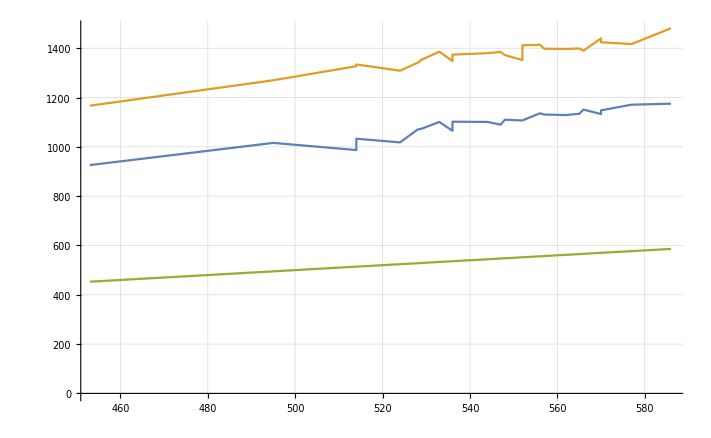

```mathematica
p100 = ListLinePlot[{min100, max100, init100}, GridLines->Automatic]
```

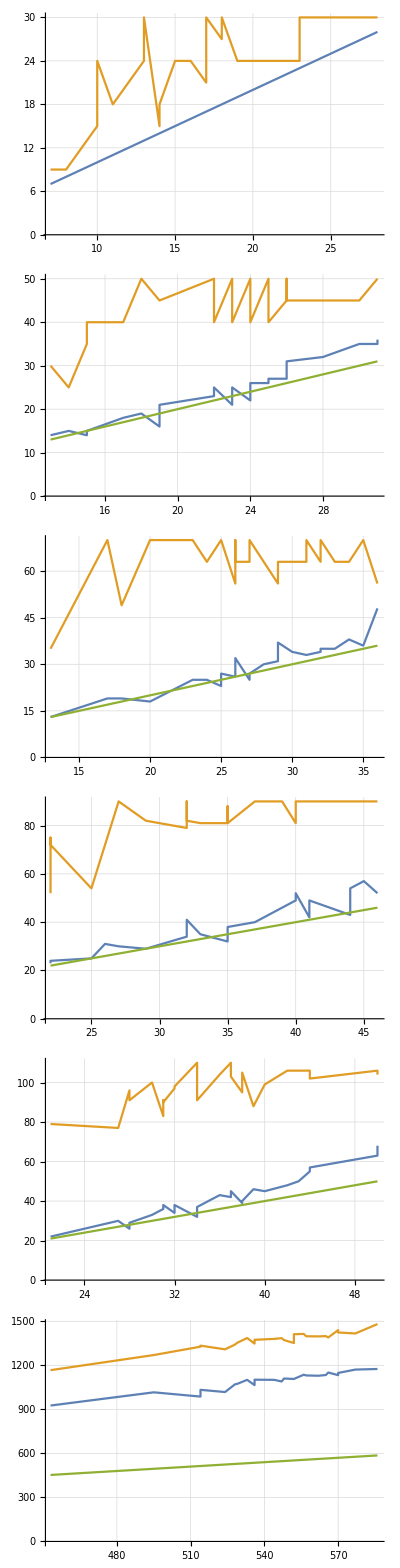

```mathematica
{p3,p4,p5,p6,p7, p100} // TableForm
```

### As the number of people crossing gets higher and higher, the chance of the minimum time it takes to cross being less than the total initial time is zero. In other words, for a large number of people crossing, the minimum time (and maximum time) is a linear positive offset of the total initial time.